## Primer

### 1.1.1 Paths in Euclidean space

Figure 1

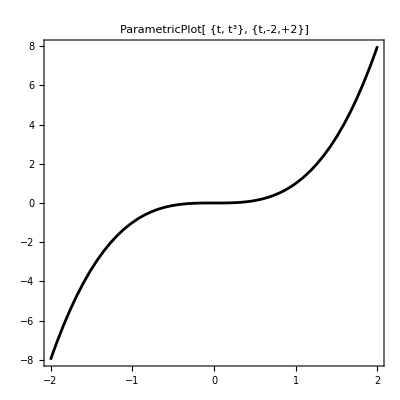

```mathematica
ParametricPlot[{t,t^3},{t,-2,2},Frame->True,AspectRatio->1,
AxesStyle->{{Dashed,Gray},{Dashed,Gray}},PlotStyle->Black,
PlotLabel->Style[Framed["ParametricPlot[ {t, t^3}, {t,-2,+2}]"],16]]
```

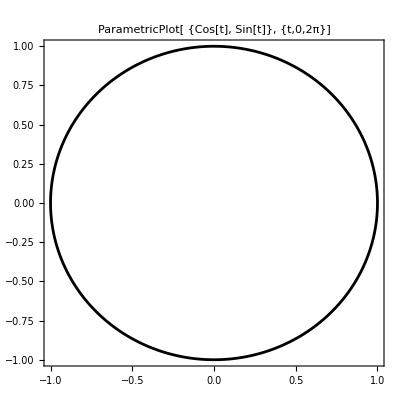

```mathematica
ParametricPlot[{Cos[t],Sin[t]},{t,0,2π},Frame->True,AspectRatio->1,
AxesStyle->{{Dashed,Gray},{Dashed,Gray}},PlotStyle->Black,
PlotLabel->Style[Framed["ParametricPlot[ {Cos[t], Sin[t]}, {t,0,2π}]"],16]]
```

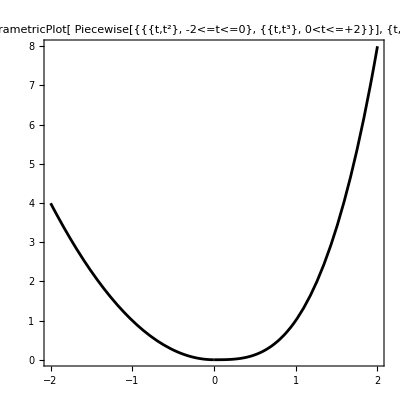

```mathematica
ParametricPlot[Piecewise[{{{t,t^2}, -2<=t<=0}, {{t,t^3}, 0<t<=+2}}],{t,-2,2},Frame->True,AspectRatio->1,
AxesStyle->{{Dashed,Gray},{Dashed,Gray}},PlotStyle->Black,
PlotLabel->Style[Framed["ParametricPlot[ Piecewise[{{{t,t^2}, -2<=t<=0}, {{t,t^3}, 0<t<=+2}}], {t,-2,+2}]"],16]]
```

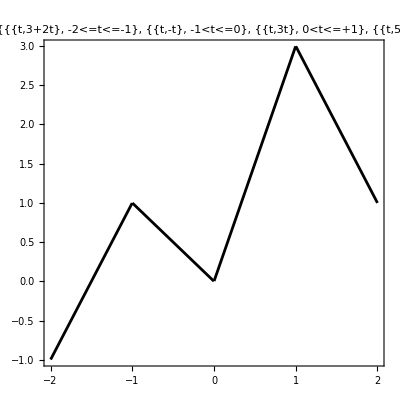

```mathematica
ParametricPlot[Piecewise[{{{t,3+2t}, -2<=t<=-1}, {{t,-t}, -1<t<=0}, {{t,3t}, 0<t<=+1}, {{t,5-2t}, +1<t<=+2}}],{t,-2,2},Frame->True,AspectRatio->1,
AxesStyle->{{Dashed,Gray},{Dashed,Gray}},PlotStyle->Black,
PlotLabel->Style[Framed["ParametricPlot[ Piecewise[{{{t,3+2t}, -2<=t<=-1}, {{t,-t}, -1<t<=0}, {{t,3t}, 0<t<=+1}, {{t,5-2t}, +1<t<=+2}}], {t,-2,+2}]"],16]]
```

### 1.1.2 Path integrals

The scalar line integral of the function f along a curve C={r(u)∈ℝ^n,a≤u≤b} is given by:

-Graphics-"∮_C f(x)ⅆx=∫_a^b f(r(u)) Norm[r'(u)]ⅆu"

∫_a^b f(X_t) ⅆ X_t=∫_a^b f(X_t) ⅆt=∫_a^b f(X_t)dX_t/dt ⅆt

```mathematica
LineIntegrate[t^2,{x}∈ParametricRegion[{t^3},{{t,0,1}}]]
```

3/5

```mathematica
nrsign[d_,k_]:=If[d==1,k+1,(d^(k+1)-1)/(d-1)];
```

```mathematica
Table[nrsign[2,k]-1,{k,1,12}]
```

{2,6,14,30,62,126,254,510,1022,2046,4094,8190}

### 1.2.2 Examples

```mathematica
iterinteg[functions_,limits_,assumptions_]:=Fold[Integrate[#1*#2[[1]],#2[[2]],Assumptions->assumptions]&,1,Transpose[{functions,limits}]];
```

```mathematica
tensorfold[list_,dim_:2]:=If[Length[list]>=dim,ArrayReshape[list,ConstantArray[dim,Log[dim,Length[list]]]],list];
```

```mathematica
Map[tensorfold,{{1},{5,55},{25/2,475/3,350/3,3025/2},{125/6,1125/4,1375/6,18875/6,2125/12,7250/3,2000,166375/6}}]
```

{{1},{5,55},{{25/2,475/3},{350/3,3025/2}},{{{125/6,1125/4},{1375/6,18875/6}},{{2125/12,7250/3},{2000,166375/6}}}}

```mathematica
signat[paths_,limits_,level_:3]:=Module[{dpaths,dpathsf,integrands,ilimits,iassump,results},
dpaths=D[paths,t];
dpathsf=Map[Function[t,#]&,dpaths,{2}];
integrands=Table[Map[Tuples,Transpose[Table[Map[#[Subscript[t, j]]&,dpathsf,{2}],{j,1,k}]]],{k,1,level}];
ilimits=Table[Table[{Subscript[t, j],limits[[1]],If[j==k,limits[[2]],Subscript[t, j+1]]},{j,1,k}],{k,1,level}];
iassump=Fold[(#1&&(limits[[1]]<=Subscript[t, #2]<=limits[[2]]))&,(limits[[1]]<=Subscript[t, 1]<=limits[[2]]),Range[2,level]];
results=Table[Map[iterinteg[#,ilimits[[k]],iassump]&,integrands[[k]],{2}],{k,1,level}];
Map[tensorfold,Map[Prepend[#,{1}]&,Transpose[results]],{2}]
];
```

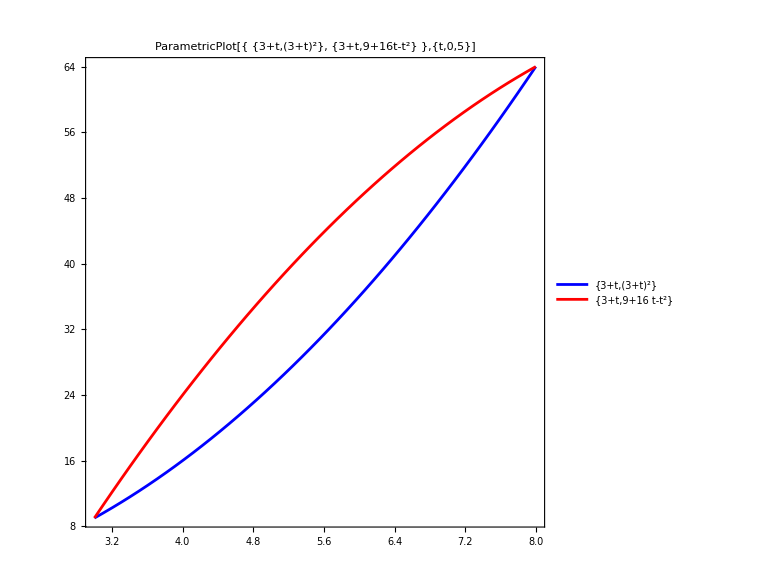

```mathematica
ParametricPlot[{{3+t,(3+t)^2},{3+t,9+16t-t^2}},{t,0,5},
Frame->True,AspectRatio->1,PlotLegends->"Expressions",
ImageSize->Large,AxesStyle->{{Dashed,Gray},{Dashed,Gray}},
AxesOrigin->{3,9},PlotStyle->{Blue,Red},
PlotLabel->Style[Framed[
"ParametricPlot[{
{3+t,(3+t)^2},
{3+t,9+16t-t^2}
},{t,0,5}]"],16]]
```

```mathematica
signat[{{3+t,(3+t)^2},{3+t,9+16t-t^2}},{0,5}]
```

{{{1},{5,55},{{25/2,475/3},{350/3,3025/2}},{{{125/6,1125/4},{1375/6,18875/6}},{{2125/12,7250/3},{2000,166375/6}}}},{{1},{5,55},{{25/2,350/3},{475/3,3025/2}},{{{125/6,2125/12},{1375/6,2000}},{{1125/4,7250/3},{18875/6,166375/6}}}}}

### Sin

#### Plot and Signatures

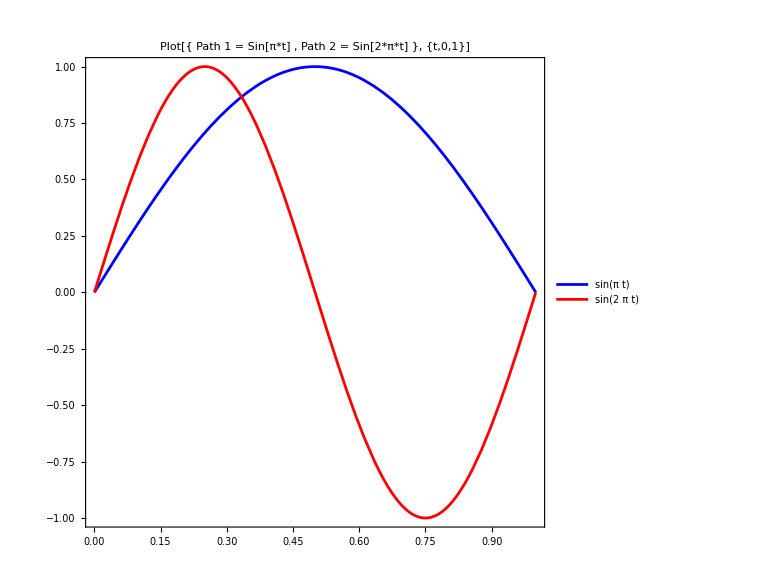

```mathematica
Plot[{Sin[π t],Sin[2π t]},{t,0,1},Frame->True,
PlotRange->All,PlotLegends->"Expressions",AspectRatio->1,
ImageSize->Large,AxesStyle->{{Dashed,Gray},{Dashed,Gray}},
PlotStyle->{Blue,Red},
PlotLabel->Style[Framed[
"Plot[{
Path 1 = Sin[π*t] ,
Path 2 = Sin[2*π*t] 
}, {t,0,1}]"],16]]
```

```mathematica
Timing[sigsins=signat[{{t,Sin[π t]},{t,Sin[2π t]}},{0,1},5]]
```

{135.83,{{{1},{1,0},{{1/2,-2/π},{2/π,0}},{{{1/6,-1/π},{0,1/4}},{{1/π,-1/2},{1/4,0}}},{{{{1/24,-(-4+π^2)/(2 π^3)},{(-12+π^2)/(2 π^3),1/8}},{{-(-12+π^2)/(2 π^3),-1/4+2/π^2},{1/4-2/π^2,-2/(9 π)}}},{{{(-4+π^2)/(2 π^3),-2/π^2},{-1/4+2/π^2,2/(3 π)}},{{1/8,-2/(3 π)},{2/(9 π),0}}}},{{{{{1/120,1/π^3-1/(6 π)},{(-12+π^2)/(6 π^3),1/48 (2-3/π^2)}},{{0,-1/12+7/(8 π^2)},{1/48 (4-33/π^2),-1/(9 π)}}},{{{-(-12+π^2)/(6 π^3),-1/(4 π^2)},{-1/12+3/(4 π^2),1/(12 π)}},{{1/48 (4-33/π^2),-1/(12 π)},{0,1/64}}}},{{{{(-6+π^2)/(6 π^3),-1/(2 π^2)},{-1/(4 π^2),1/(4 π)}},{{-1/12+7/(8 π^2),0},{1/(12 π),-1/16}}},{{{1/48 (2-3/π^2),-1/(4 π)},{-1/(12 π),3/32}},{{1/(9 π),-1/16},{1/64,0}}}}}},{{1},{1,0},{{1/2,0},{0,0}},{{{1/6,1/(2 π)},{-1/π,1/4}},{{1/(2 π),-1/2},{1/4,0}}},{{{{1/24,1/(4 π)},{-1/(4 π),1/8}},{{-1/(4 π),-1/4},{1/4,0}}},{{{1/(4 π),0},{-1/4,0}},{{1/8,0},{0,0}}}},{{{{{1/120,(-3+2 π^2)/(24 π^3)},{-(-6+π^2)/(12 π^3),1/24-1/(64 π^2)}},{{-3/(4 π^3),-1/12+7/(32 π^2)},{1/12-11/(64 π^2),1/(18 π)}}},{{{-(-6+π^2)/(12 π^3),-9/(16 π^2)},{1/48 (-4+33/π^2),-7/(24 π)}},{{1/12-11/(64 π^2),13/(24 π)},{-13/(36 π),1/64}}}},{{{{(-3+2 π^2)/(24 π^3),3/(8 π^2)},{-9/(16 π^2),1/(8 π)}},{{-1/12+7/(32 π^2),-1/(2 π)},{13/(24 π),-1/16}}},{{{1/24-1/(64 π^2),1/(8 π)},{-7/(24 π),3/32}},{{1/(18 π),-1/16},{1/64,0}}}}}}}}

```mathematica
{sigsins1f,sigsins2f}=sigsins;
```

```mathematica
sigsins1f
```

{{1},{1,0},{{1/2,-2/π},{2/π,0}},{{{1/6,-1/π},{0,1/4}},{{1/π,-1/2},{1/4,0}}},{{{{1/24,-(-4+π^2)/(2 π^3)},{(-12+π^2)/(2 π^3),1/8}},{{-(-12+π^2)/(2 π^3),-1/4+2/π^2},{1/4-2/π^2,-2/(9 π)}}},{{{(-4+π^2)/(2 π^3),-2/π^2},{-1/4+2/π^2,2/(3 π)}},{{1/8,-2/(3 π)},{2/(9 π),0}}}},{{{{{1/120,1/π^3-1/(6 π)},{(-12+π^2)/(6 π^3),1/48 (2-3/π^2)}},{{0,-1/12+7/(8 π^2)},{1/48 (4-33/π^2),-1/(9 π)}}},{{{-(-12+π^2)/(6 π^3),-1/(4 π^2)},{-1/12+3/(4 π^2),1/(12 π)}},{{1/48 (4-33/π^2),-1/(12 π)},{0,1/64}}}},{{{{(-6+π^2)/(6 π^3),-1/(2 π^2)},{-1/(4 π^2),1/(4 π)}},{{-1/12+7/(8 π^2),0},{1/(12 π),-1/16}}},{{{1/48 (2-3/π^2),-1/(4 π)},{-1/(12 π),3/32}},{{1/(9 π),-1/16},{1/64,0}}}}}}

```mathematica
sigsins1f[[5]]
```

{{{{1/24,-(-4+π^2)/(2 π^3)},{(-12+π^2)/(2 π^3),1/8}},{{-(-12+π^2)/(2 π^3),-1/4+2/π^2},{1/4-2/π^2,-2/(9 π)}}},{{{(-4+π^2)/(2 π^3),-2/π^2},{-1/4+2/π^2,2/(3 π)}},{{1/8,-2/(3 π)},{2/(9 π),0}}}}

```mathematica
sigsins2f
```

{{1},{1,0},{{1/2,0},{0,0}},{{{1/6,1/(2 π)},{-1/π,1/4}},{{1/(2 π),-1/2},{1/4,0}}},{{{{1/24,1/(4 π)},{-1/(4 π),1/8}},{{-1/(4 π),-1/4},{1/4,0}}},{{{1/(4 π),0},{-1/4,0}},{{1/8,0},{0,0}}}},{{{{{1/120,(-3+2 π^2)/(24 π^3)},{-(-6+π^2)/(12 π^3),1/24-1/(64 π^2)}},{{-3/(4 π^3),-1/12+7/(32 π^2)},{1/12-11/(64 π^2),1/(18 π)}}},{{{-(-6+π^2)/(12 π^3),-9/(16 π^2)},{1/48 (-4+33/π^2),-7/(24 π)}},{{1/12-11/(64 π^2),13/(24 π)},{-13/(36 π),1/64}}}},{{{{(-3+2 π^2)/(24 π^3),3/(8 π^2)},{-9/(16 π^2),1/(8 π)}},{{-1/12+7/(32 π^2),-1/(2 π)},{13/(24 π),-1/16}}},{{{1/24-1/(64 π^2),1/(8 π)},{-7/(24 π),3/32}},{{1/(18 π),-1/16},{1/64,0}}}}}}

```mathematica
sigsins2f[[5]]
```

{{{{1/24,1/(4 π)},{-1/(4 π),1/8}},{{-1/(4 π),-1/4},{1/4,0}}},{{{1/(4 π),0},{-1/4,0}},{{1/8,0},{0,0}}}}

```mathematica
N[sigsins1f]
```

{{1.},{1.,0.},{{0.5,-0.63662},{0.63662,0.}},{{{0.166667,-0.31831},{0.,0.25}},{{0.31831,-0.5},{0.25,0.}}},{{{{0.0416667,-0.0946519},{-0.0343543,0.125}},{{0.0343543,-0.0473576},{0.0473576,-0.0707355}}},{{{0.0946519,-0.202642},{-0.0473576,0.212207}},{{0.125,-0.212207},{0.0707355,0.}}}},{{{{{0.00833333,-0.0208001},{-0.0114514,0.0353341}},{{0.,0.0053227},{0.013675,-0.0353678}}},{{{0.0114514,-0.0253303},{-0.00734245,0.0265258}},{{0.013675,-0.0265258},{0.,0.015625}}}},{{{{0.0208001,-0.0506606},{-0.0253303,0.0795775}},{{0.0053227,0.},{0.0265258,-0.0625}}},{{{0.0353341,-0.0795775},{-0.0265258,0.09375}},{{0.0353678,-0.0625},{0.015625,0.}}}}}}

```mathematica
N[sigsins1f[[5]]]
```

{{{{0.0416667,-0.0946519},{-0.0343543,0.125}},{{0.0343543,-0.0473576},{0.0473576,-0.0707355}}},{{{0.0946519,-0.202642},{-0.0473576,0.212207}},{{0.125,-0.212207},{0.0707355,0.}}}}

```mathematica
N[sigsins2f]
```

{{1.},{1.,0.},{{0.5,0.},{0.,0.}},{{{0.166667,0.159155},{-0.31831,0.25}},{{0.159155,-0.5},{0.25,0.}}},{{{{0.0416667,0.0795775},{-0.0795775,0.125}},{{-0.0795775,-0.25},{0.25,0.}}},{{{0.0795775,0.},{-0.25,0.}},{{0.125,0.},{0.,0.}}}},{{{{{0.00833333,0.0224944},{-0.0104001,0.0400835}},{{-0.0241887,-0.0611693},{0.0659188,0.0176839}}},{{{-0.0104001,-0.0569932},{-0.013675,-0.0928404}},{{0.0659188,0.172418},{-0.114945,0.015625}}}},{{{{0.0224944,0.0379954},{-0.0569932,0.0397887}},{{-0.0611693,-0.159155},{0.172418,-0.0625}}},{{{0.0400835,0.0397887},{-0.0928404,0.09375}},{{0.0176839,-0.0625},{0.015625,0.}}}}}}

```mathematica
N[sigsins2f[[5]]]
```

{{{{0.0416667,0.0795775},{-0.0795775,0.125}},{{-0.0795775,-0.25},{0.25,0.}}},{{{0.0795775,0.},{-0.25,0.}},{{0.125,0.},{0.,0.}}}}

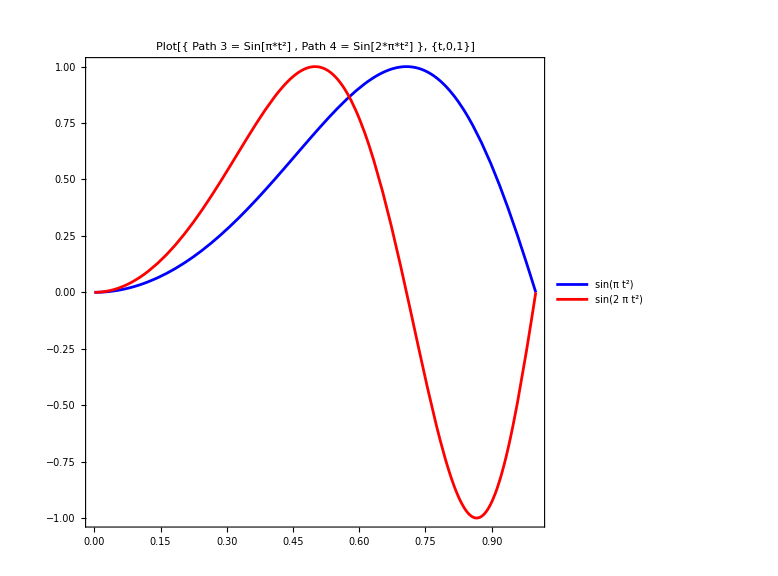

```mathematica
Plot[{Sin[π t^2],Sin[2π t^2]},{t,0,1},Frame->True,
PlotRange->All,PlotLegends->"Expressions",AspectRatio->1,
ImageSize->Large,AxesStyle->{{Dashed,Gray},{Dashed,Gray}},
PlotStyle->{Blue,Red},
PlotLabel->Style[Framed[
"Plot[{
Path 3 = Sin[π*t^2] ,
Path 4 = Sin[2*π*t^2]
}, {t,0,1}]"],16]]
```

```mathematica
Timing[sigsins2=signat[{{t,Sin[π t^2]},{t,Sin[2π t^2]}},{0,1},4]]
```

{42.2397,{{{1},{1,0},{{1/2,-FresnelS[√2]/(√2)},{FresnelS[√2]/(√2),0}},{{{1/6,-1/π},{2/π-FresnelS[√2]/(√2),1/8 (2-FresnelC[2])}},{{-1/π+FresnelS[√2]/(√2),1/4 (-2+FresnelC[2])},{1/8 (2-FresnelC[2]),0}}},{{{{1/24,-(2+√2 FresnelC[√2])/(8 π)},{(-2+3 √2 FresnelC[√2])/(8 π),1/8}},{{(10-3 √2 FresnelC[√2]-2 √2 π FresnelS[√2])/(8 π),1/4 (-1+FresnelS[√2]^2)},{1/8 (2-FresnelC[2]-2 FresnelS[√2]^2),1/144 (-9 √2 FresnelS[√2]+√6 FresnelS[√6])}}},{{{(-6+√2 FresnelC[√2]+2 √2 π FresnelS[√2])/(8 π),-1/4 FresnelS[√2]^2},{1/4 (-1+FresnelC[2]+FresnelS[√2]^2),1/48 (9 √2 FresnelS[√2]-√6 FresnelS[√6])}},{{1/8 (1-FresnelC[2]),1/48 (-9 √2 FresnelS[√2]+√6 FresnelS[√6])},{(3 √3 FresnelS[√2]-FresnelS[√6])/(24 √6),0}}}}},{{1},{1,0},{{1/2,-FresnelS[2]/2},{FresnelS[2]/2,0}},{{{1/6,0},{-FresnelS[2]/2,1/16 (4-√2 FresnelC[2 √2])}},{{FresnelS[2]/2,1/8 (-4+√2 FresnelC[2 √2])},{1/16 (4-√2 FresnelC[2 √2]),0}}},{{{{1/24,-(-2+FresnelC[2])/(16 π)},{(3 (-2+FresnelC[2]))/(16 π),1/8}},{{(6-3 FresnelC[2]-4 π FresnelS[2])/(16 π),1/8 (-2+FresnelS[2]^2)},{1/16 (4-√2 FresnelC[2 √2]-2 FresnelS[2]^2),1/144 (-9 FresnelS[2]+√3 FresnelS[2 √3])}}},{{{(-2+FresnelC[2]+4 π FresnelS[2])/(16 π),-1/8 FresnelS[2]^2},{1/8 (-2+√2 FresnelC[2 √2]+FresnelS[2]^2),1/48 (9 FresnelS[2]-√3 FresnelS[2 √3])}},{{1/16 (2-√2 FresnelC[2 √2]),1/48 (-9 FresnelS[2]+√3 FresnelS[2 √3])},{1/144 (9 FresnelS[2]-√3 FresnelS[2 √3]),0}}}}}}}

```mathematica
{sigsins1f2,sigsins2f2}=sigsins2;
```

```mathematica
sigsins1f2
```

{{1},{1,0},{{1/2,-FresnelS[√2]/(√2)},{FresnelS[√2]/(√2),0}},{{{1/6,-1/π},{2/π-FresnelS[√2]/(√2),1/8 (2-FresnelC[2])}},{{-1/π+FresnelS[√2]/(√2),1/4 (-2+FresnelC[2])},{1/8 (2-FresnelC[2]),0}}},{{{{1/24,-(2+√2 FresnelC[√2])/(8 π)},{(-2+3 √2 FresnelC[√2])/(8 π),1/8}},{{(10-3 √2 FresnelC[√2]-2 √2 π FresnelS[√2])/(8 π),1/4 (-1+FresnelS[√2]^2)},{1/8 (2-FresnelC[2]-2 FresnelS[√2]^2),1/144 (-9 √2 FresnelS[√2]+√6 FresnelS[√6])}}},{{{(-6+√2 FresnelC[√2]+2 √2 π FresnelS[√2])/(8 π),-1/4 FresnelS[√2]^2},{1/4 (-1+FresnelC[2]+FresnelS[√2]^2),1/48 (9 √2 FresnelS[√2]-√6 FresnelS[√6])}},{{1/8 (1-FresnelC[2]),1/48 (-9 √2 FresnelS[√2]+√6 FresnelS[√6])},{(3 √3 FresnelS[√2]-FresnelS[√6])/(24 √6),0}}}}}

```mathematica
sigsins2f2
```

{{1},{1,0},{{1/2,-FresnelS[2]/2},{FresnelS[2]/2,0}},{{{1/6,0},{-FresnelS[2]/2,1/16 (4-√2 FresnelC[2 √2])}},{{FresnelS[2]/2,1/8 (-4+√2 FresnelC[2 √2])},{1/16 (4-√2 FresnelC[2 √2]),0}}},{{{{1/24,-(-2+FresnelC[2])/(16 π)},{(3 (-2+FresnelC[2]))/(16 π),1/8}},{{(6-3 FresnelC[2]-4 π FresnelS[2])/(16 π),1/8 (-2+FresnelS[2]^2)},{1/16 (4-√2 FresnelC[2 √2]-2 FresnelS[2]^2),1/144 (-9 FresnelS[2]+√3 FresnelS[2 √3])}}},{{{(-2+FresnelC[2]+4 π FresnelS[2])/(16 π),-1/8 FresnelS[2]^2},{1/8 (-2+√2 FresnelC[2 √2]+FresnelS[2]^2),1/48 (9 FresnelS[2]-√3 FresnelS[2 √3])}},{{1/16 (2-√2 FresnelC[2 √2]),1/48 (-9 FresnelS[2]+√3 FresnelS[2 √3])},{1/144 (9 FresnelS[2]-√3 FresnelS[2 √3]),0}}}}}

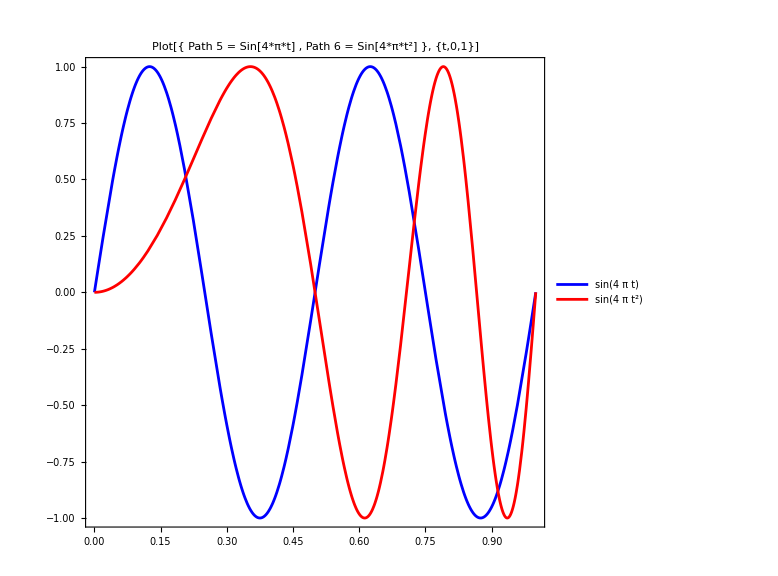

```mathematica
Plot[{Sin[4π t],Sin[4π t^2]},{t,0,1},Frame->True,
PlotRange->All,PlotLegends->"Expressions",AspectRatio->1,
ImageSize->Large,AxesStyle->{{Dashed,Gray},{Dashed,Gray}},
PlotStyle->{Blue,Red},
PlotLabel->Style[Framed[
"Plot[{
Path 5 = Sin[4*π*t] ,
Path 6 = Sin[4*π*t^2]
}, {t,0,1}]"],16]]
```

```mathematica
Timing[sigsins42=signat[{{t,Sin[4π t]},{t,Sin[4π t^2]}},{0,1},4]]
```

{46.8146,{{{1},{1,0},{{1/2,0},{0,0}},{{{1/6,1/(4 π)},{-1/(2 π),1/4}},{{1/(4 π),-1/2},{1/4,0}}},{{{{1/24,1/(8 π)},{-1/(8 π),1/8}},{{-1/(8 π),-1/4},{1/4,0}}},{{{1/(8 π),0},{-1/4,0}},{{1/8,0},{0,0}}}}},{{1},{1,0},{{1/2,-FresnelS[2 √2]/(2 √2)},{FresnelS[2 √2]/(2 √2),0}},{{{1/6,0},{-FresnelS[2 √2]/(2 √2),1/16 (4-FresnelC[4])}},{{FresnelS[2 √2]/(2 √2),1/8 (-4+FresnelC[4])},{1/16 (4-FresnelC[4]),0}}},{{{{1/24,(4-√2 FresnelC[2 √2])/(64 π)},{(3 (-4+√2 FresnelC[2 √2]))/(64 π),1/8}},{{(12-3 √2 FresnelC[2 √2]-8 √2 π FresnelS[2 √2])/(64 π),1/16 (-4+FresnelS[2 √2]^2)},{1/16 (4-FresnelC[4]-FresnelS[2 √2]^2),1/288 (-9 √2 FresnelS[2 √2]+√6 FresnelS[2 √6])}}},{{{(-4+√2 FresnelC[2 √2]+8 √2 π FresnelS[2 √2])/(64 π),-1/16 FresnelS[2 √2]^2},{1/16 (-4+2 FresnelC[4]+FresnelS[2 √2]^2),1/96 (9 √2 FresnelS[2 √2]-√6 FresnelS[2 √6])}},{{1/16 (2-FresnelC[4]),1/96 (-9 √2 FresnelS[2 √2]+√6 FresnelS[2 √6])},{(3 √3 FresnelS[2 √2]-FresnelS[2 √6])/(48 √6),0}}}}}}}

```mathematica
{sigsins1f42,sigsins2f42}=sigsins42;
```

```mathematica
sigsins1f42
```

{{1},{1,0},{{1/2,0},{0,0}},{{{1/6,1/(4 π)},{-1/(2 π),1/4}},{{1/(4 π),-1/2},{1/4,0}}},{{{{1/24,1/(8 π)},{-1/(8 π),1/8}},{{-1/(8 π),-1/4},{1/4,0}}},{{{1/(8 π),0},{-1/4,0}},{{1/8,0},{0,0}}}}}

```mathematica
sigsins2f42
```

{{1},{1,0},{{1/2,-FresnelS[2 √2]/(2 √2)},{FresnelS[2 √2]/(2 √2),0}},{{{1/6,0},{-FresnelS[2 √2]/(2 √2),1/16 (4-FresnelC[4])}},{{FresnelS[2 √2]/(2 √2),1/8 (-4+FresnelC[4])},{1/16 (4-FresnelC[4]),0}}},{{{{1/24,(4-√2 FresnelC[2 √2])/(64 π)},{(3 (-4+√2 FresnelC[2 √2]))/(64 π),1/8}},{{(12-3 √2 FresnelC[2 √2]-8 √2 π FresnelS[2 √2])/(64 π),1/16 (-4+FresnelS[2 √2]^2)},{1/16 (4-FresnelC[4]-FresnelS[2 √2]^2),1/288 (-9 √2 FresnelS[2 √2]+√6 FresnelS[2 √6])}}},{{{(-4+√2 FresnelC[2 √2]+8 √2 π FresnelS[2 √2])/(64 π),-1/16 FresnelS[2 √2]^2},{1/16 (-4+2 FresnelC[4]+FresnelS[2 √2]^2),1/96 (9 √2 FresnelS[2 √2]-√6 FresnelS[2 √6])}},{{1/16 (2-FresnelC[4]),1/96 (-9 √2 FresnelS[2 √2]+√6 FresnelS[2 √6])},{(3 √3 FresnelS[2 √2]-FresnelS[2 √6])/(48 √6),0}}}}}

```mathematica
N[sigsins1f42]
```

{{1.},{1.,0.},{{0.5,0.},{0.,0.}},{{{0.166667,0.0795775},{-0.159155,0.25}},{{0.0795775,-0.5},{0.25,0.}}},{{{{0.0416667,0.0397887},{-0.0397887,0.125}},{{-0.0397887,-0.25},{0.25,0.}}},{{{0.0397887,0.},{-0.25,0.}},{{0.125,0.},{0.,0.}}}}}

```mathematica
N[sigsins2f42]
```

{{1.},{1.,0.},{{0.5,-0.137168},{0.137168,0.}},{{{0.166667,0.},{-0.137168,0.218848}},{{0.137168,-0.437697},{0.218848,0.}}},{{{{0.0416667,0.0164083},{-0.049225,0.125}},{{-0.0193589,-0.240593},{0.209441,-0.0134457}}},{{{0.0521756,-0.0094075},{-0.178289,0.0403371}},{{0.0938484,-0.0403371},{0.0134457,0.}}}}}

```mathematica
Grid[{{sigsins1f[[2]]},{sigsins2f[[2]]},{sigsins1f2[[2]]},{sigsins2f2[[2]]},{sigsins1f42[[2]]},{sigsins2f42[[2]]}}]
```

{1,0}
{1,0}
{1,0}
{1,0}
{1,0}
{1,0}

```mathematica
Grid[{{sigsins1f[[3]]},{sigsins2f[[3]]},{sigsins1f2[[3]]},{sigsins2f2[[3]]},{sigsins1f42[[3]]},{sigsins2f42[[3]]}},Frame->All]
```

{{1/2,-2/π},{2/π,0}}
{{1/2,0},{0,0}}
{{1/2,-FresnelS[√2]/(√2)},{FresnelS[√2]/(√2),0}}
{{1/2,-FresnelS[2]/2},{FresnelS[2]/2,0}}
{{1/2,0},{0,0}}
{{1/2,-FresnelS[2 √2]/(2 √2)},{FresnelS[2 √2]/(2 √2),0}}

```mathematica
Grid[Expand[{{sigsins1f[[4]]},{sigsins2f[[4]]},{sigsins1f2[[4]]},{sigsins2f2[[4]]},{sigsins1f42[[4]]},{sigsins2f42[[4]]}}],Frame->All]
```

{{{1/6,-1/π},{0,1/4}},{{1/π,-1/2},{1/4,0}}}
{{{1/6,1/(2 π)},{-1/π,1/4}},{{1/(2 π),-1/2},{1/4,0}}}
{{{1/6,-1/π},{2/π-FresnelS[√2]/(√2),1/4-FresnelC[2]/8}},{{-1/π+FresnelS[√2]/(√2),-1/2+FresnelC[2]/4},{1/4-FresnelC[2]/8,0}}}
{{{1/6,0},{-FresnelS[2]/2,1/4-FresnelC[2 √2]/(8 √2)}},{{FresnelS[2]/2,-1/2+FresnelC[2 √2]/(4 √2)},{1/4-FresnelC[2 √2]/(8 √2),0}}}
{{{1/6,1/(4 π)},{-1/(2 π),1/4}},{{1/(4 π),-1/2},{1/4,0}}}
{{{1/6,0},{-FresnelS[2 √2]/(2 √2),1/4-FresnelC[4]/16}},{{FresnelS[2 √2]/(2 √2),-1/2+FresnelC[4]/8},{1/4-FresnelC[4]/16,0}}}

```mathematica
Grid[Expand[{{sigsins1f[[5]]},{sigsins2f[[5]]},{sigsins1f2[[5]]},{sigsins2f2[[5]]},{sigsins1f42[[5]]},{sigsins2f42[[5]]}}],Frame->All]
```

{{{{1/24,2/π^3-1/(2 π)},{-6/π^3+1/(2 π),1/8}},{{6/π^3-1/(2 π),-1/4+2/π^2},{1/4-2/π^2,-2/(9 π)}}},{{{-2/π^3+1/(2 π),-2/π^2},{-1/4+2/π^2,2/(3 π)}},{{1/8,-2/(3 π)},{2/(9 π),0}}}}
{{{{1/24,1/(4 π)},{-1/(4 π),1/8}},{{-1/(4 π),-1/4},{1/4,0}}},{{{1/(4 π),0},{-1/4,0}},{{1/8,0},{0,0}}}}
{{{{1/24,-1/(4 π)-FresnelC[√2]/(4 √2 π)},{-1/(4 π)+(3 FresnelC[√2])/(4 √2 π),1/8}},{{5/(4 π)-(3 FresnelC[√2])/(4 √2 π)-FresnelS[√2]/(2 √2),-1/4+1/4 FresnelS[√2]^2},{1/4-FresnelC[2]/8-1/4 FresnelS[√2]^2,-FresnelS[√2]/(8 √2)+FresnelS[√6]/(24 √6)}}},{{{-3/(4 π)+FresnelC[√2]/(4 √2 π)+FresnelS[√2]/(2 √2),-1/4 FresnelS[√2]^2},{-1/4+FresnelC[2]/4+1/4 FresnelS[√2]^2,(3 FresnelS[√2])/(8 √2)-FresnelS[√6]/(8 √6)}},{{1/8-FresnelC[2]/8,-(3 FresnelS[√2])/(8 √2)+FresnelS[√6]/(8 √6)},{FresnelS[√2]/(8 √2)-FresnelS[√6]/(24 √6),0}}}}
{{{{1/24,1/(8 π)-FresnelC[2]/(16 π)},{-3/(8 π)+(3 FresnelC[2])/(16 π),1/8}},{{3/(8 π)-(3 FresnelC[2])/(16 π)-FresnelS[2]/4,-1/4+FresnelS[2]^2/8},{1/4-FresnelC[2 √2]/(8 √2)-FresnelS[2]^2/8,-FresnelS[2]/16+FresnelS[2 √3]/(48 √3)}}},{{{-1/(8 π)+FresnelC[2]/(16 π)+FresnelS[2]/4,-1/8 FresnelS[2]^2},{-1/4+FresnelC[2 √2]/(4 √2)+FresnelS[2]^2/8,(3 FresnelS[2])/16-FresnelS[2 √3]/(16 √3)}},{{1/8-FresnelC[2 √2]/(8 √2),-(3 FresnelS[2])/16+FresnelS[2 √3]/(16 √3)},{FresnelS[2]/16-FresnelS[2 √3]/(48 √3),0}}}}
{{{{1/24,1/(8 π)},{-1/(8 π),1/8}},{{-1/(8 π),-1/4},{1/4,0}}},{{{1/(8 π),0},{-1/4,0}},{{1/8,0},{0,0}}}}
{{{{1/24,1/(16 π)-FresnelC[2 √2]/(32 √2 π)},{-3/(16 π)+(3 FresnelC[2 √2])/(32 √2 π),1/8}},{{3/(16 π)-(3 FresnelC[2 √2])/(32 √2 π)-FresnelS[2 √2]/(4 √2),-1/4+1/16 FresnelS[2 √2]^2},{1/4-FresnelC[4]/16-1/16 FresnelS[2 √2]^2,-FresnelS[2 √2]/(16 √2)+FresnelS[2 √6]/(48 √6)}}},{{{-1/(16 π)+FresnelC[2 √2]/(32 √2 π)+FresnelS[2 √2]/(4 √2),-1/16 FresnelS[2 √2]^2},{-1/4+FresnelC[4]/8+1/16 FresnelS[2 √2]^2,(3 FresnelS[2 √2])/(16 √2)-FresnelS[2 √6]/(16 √6)}},{{1/8-FresnelC[4]/16,-(3 FresnelS[2 √2])/(16 √2)+FresnelS[2 √6]/(16 √6)},{FresnelS[2 √2]/(16 √2)-FresnelS[2 √6]/(48 √6),0}}}}

```mathematica
Timing[sigline=signat[{{Subscript[a, 1]+Subscript[b, 1]*t,Subscript[a, 2]+Subscript[b, 2]*t}},{0,T},2]]
```

{0.001902,{{{1},{T b_1,T b_2},{{1/2 T^2 b_1^2,1/2 T^2 b_1 b_2},{1/2 T^2 b_1 b_2,1/2 T^2 b_2^2}}}}}

## Shuffle Product

### Typesetting

Enter ⧢

```mathematica
{1,2}⧢{a}={{a,1,2},{1,a,2},{1,2,a}}
```

### Functions

#### Much better shuffle product (Mathematica Stack Exchange)

```mathematica
shp[u:{a_,x___},v:{b_,y___},c___]:=Join[shp[{x},v,c,a],shp[u,{y},c,b]];
shp[{x___},{y___},c___]:={{c,x,y}} ;(*rule for empty-set termination*)
```

```mathematica
shp[{1,2},{3}]
```

{{1,2,3},{1,3,2},{3,1,2}}

```mathematica
shp[{1,2},{2,1}]
```

{{1,2,2,1},{1,2,2,1},{1,2,1,2},{2,1,2,1},{2,1,1,2},{2,1,1,2}}

```mathematica
Timing[Map[Length,
{shp[{a},{f}],
shp[{a,b},{f,g}],
shp[{a,b,c},{f,g,h}],
shp[{a,b,c,d},{f,g,h,i}],
shp[{a,b,c,d,e},{f,g,h,i,j}]}]]
```

{0.001594,{2,6,20,70,252}}

#### Subscript manipulation

```mathematica
inds[s_]:=Rest[Apply[List,s]];
```

```mathematica
sind[list_]:=Apply[Subscript,Prepend[list,s]];
```

#### Shuffle product identity

```mathematica
shuffles[set1_,set2_]:=Flatten[Table[Total[Map[sind,shp[inds[w1],inds[w2]]]]==w1 w2,{w1,set1},{w2,set2}]];
```

```mathematica
shuffles[{Subscript[s, 1],Subscript[s, 2]},{Subscript[s, 1,1],Subscript[s, 1,2],Subscript[s, 2,1],Subscript[s, 2,2]}]
```

{3 s_(1,1,1)==s_1 s_(1,1),2 s_(1,1,2)+s_(1,2,1)==s_1 s_(1,2),s_(1,2,1)+2 s_(2,1,1)==s_1 s_(2,1),s_(1,2,2)+s_(2,1,2)+s_(2,2,1)==s_1 s_(2,2),s_(1,1,2)+s_(1,2,1)+s_(2,1,1)==s_2 s_(1,1),2 s_(1,2,2)+s_(2,1,2)==s_2 s_(1,2),s_(2,1,2)+2 s_(2,2,1)==s_2 s_(2,1),3 s_(2,2,2)==s_2 s_(2,2)}

```mathematica
shufflespol[set1_,set2_]:=Flatten[Table[Total[Map[sind,shp[inds[w1],inds[w2]]]]-w1 w2,{w1,set1},{w2,set2}]];
```

```mathematica
shufflespol[{Subscript[s, 1],Subscript[s, 2]},{Subscript[s, 1,1],Subscript[s, 1,2],Subscript[s, 2,1],Subscript[s, 2,2]}]
```

{-s_1 s_(1,1)+3 s_(1,1,1),-s_1 s_(1,2)+2 s_(1,1,2)+s_(1,2,1),-s_1 s_(2,1)+s_(1,2,1)+2 s_(2,1,1),-s_1 s_(2,2)+s_(1,2,2)+s_(2,1,2)+s_(2,2,1),-s_2 s_(1,1)+s_(1,1,2)+s_(1,2,1)+s_(2,1,1),-s_2 s_(1,2)+2 s_(1,2,2)+s_(2,1,2),-s_2 s_(2,1)+s_(2,1,2)+2 s_(2,2,1),-s_2 s_(2,2)+3 s_(2,2,2)}

## Concatenation of Signatures (Chen)

### Exploring

```mathematica
vind[list_,var_:s]:=Apply[Subscript,Prepend[list,var]];
```

```mathematica
Flatten[Table[vind[{i,j},x],{i,1,2},{j,1,2}]]
```

{x_(1,1),x_(1,2),x_(2,1),x_(2,2)}

```mathematica
Table[vind[{i,j,k},x],{i,1,2},{j,1,2},{k,1,2}]
```

{{{x_(1,1,1),x_(1,1,2)},{x_(1,2,1),x_(1,2,2)}},{{x_(2,1,1),x_(2,1,2)},{x_(2,2,1),x_(2,2,2)}}}

```mathematica
tensorfold[Flatten[Table[vind[{i,j,k},x],{i,1,2},{j,1,2},{k,1,2}]]]
```

{{{x_(1,1,1),x_(1,1,2)},{x_(1,2,1),x_(1,2,2)}},{{x_(2,1,1),x_(2,1,2)},{x_(2,2,1),x_(2,2,2)}}}

```mathematica
tensorfold[Flatten[Table[vind[{i,j,k},y],{i,1,2},{j,1,2},{k,1,2}]]]
```

{{{y_(1,1,1),y_(1,1,2)},{y_(1,2,1),y_(1,2,2)}},{{y_(2,1,1),y_(2,1,2)},{y_(2,2,1),y_(2,2,2)}}}

```mathematica
tensorfold[Flatten[Table[vind[{i,j,k,l},x],{i,1,2},{j,1,2},{k,1,2},{l,1,2}]]]
```

{{{{x_(1,1,1,1),x_(1,1,1,2)},{x_(1,1,2,1),x_(1,1,2,2)}},{{x_(1,2,1,1),x_(1,2,1,2)},{x_(1,2,2,1),x_(1,2,2,2)}}},{{{x_(2,1,1,1),x_(2,1,1,2)},{x_(2,1,2,1),x_(2,1,2,2)}},{{x_(2,2,1,1),x_(2,2,1,2)},{x_(2,2,2,1),x_(2,2,2,2)}}}}

```mathematica
tensorfold[Flatten[Table[vind[{i,j,k,l},y],{i,1,2},{j,1,2},{k,1,2},{l,1,2}]]]
```

{{{{y_(1,1,1,1),y_(1,1,1,2)},{y_(1,1,2,1),y_(1,1,2,2)}},{{y_(1,2,1,1),y_(1,2,1,2)},{y_(1,2,2,1),y_(1,2,2,2)}}},{{{y_(2,1,1,1),y_(2,1,1,2)},{y_(2,1,2,1),y_(2,1,2,2)}},{{y_(2,2,1,1),y_(2,2,1,2)},{y_(2,2,2,1),y_(2,2,2,2)}}}}

```mathematica
tensorfold[Flatten[TensorProduct[
Flatten[Table[vind[{i},x],{i,1,2}]],
Flatten[Table[vind[{i},y],{i,1,2}]]]]]
```

{{x_1 y_1,x_1 y_2},{x_2 y_1,x_2 y_2}}

```mathematica
tensorfold[Flatten[TensorProduct[
Flatten[Table[vind[{i,j},x],{i,1,2},{j,1,2}]],
Flatten[Table[vind[{i},y],{i,1,2}]]]]]
```

{{{y_1 x_(1,1),y_2 x_(1,1)},{y_1 x_(1,2),y_2 x_(1,2)}},{{y_1 x_(2,1),y_2 x_(2,1)},{y_1 x_(2,2),y_2 x_(2,2)}}}

```mathematica
tensorfold[Flatten[TensorProduct[
Flatten[Table[vind[{i},x],{i,1,2}]],
Flatten[Table[vind[{i,j},y],{i,1,2},{j,1,2}]]]]]
```

{{{x_1 y_(1,1),x_1 y_(1,2)},{x_1 y_(2,1),x_1 y_(2,2)}},{{x_2 y_(1,1),x_2 y_(1,2)},{x_2 y_(2,1),x_2 y_(2,2)}}}

```mathematica
tensorfold[Flatten[TensorProduct[
Flatten[Table[vind[{i,j},x],{i,1,2},{j,1,2}]],
Flatten[Table[vind[{i,j},y],{i,1,2},{j,1,2}]]]]]
```

{{{{x_(1,1) y_(1,1),x_(1,1) y_(1,2)},{x_(1,1) y_(2,1),x_(1,1) y_(2,2)}},{{x_(1,2) y_(1,1),x_(1,2) y_(1,2)},{x_(1,2) y_(2,1),x_(1,2) y_(2,2)}}},{{{x_(2,1) y_(1,1),x_(2,1) y_(1,2)},{x_(2,1) y_(2,1),x_(2,1) y_(2,2)}},{{x_(2,2) y_(1,1),x_(2,2) y_(1,2)},{x_(2,2) y_(2,1),x_(2,2) y_(2,2)}}}}

### Functions

```mathematica
sigchen[sig1_,sig2_,levelout_:4]:=
Take[
Table[tensorfold[Sum[Flatten[TensorProduct[sig1[[k]],sig2[[j+1-k]]]],
{k,1,j}]],{j,1,Length[sig1]}]
,levelout+1];
```

```mathematica
chainchen[sigs_,levelout_:4]:=
Fold[sigchen[#1,#2,levelout]&,sigs[[1]],Rest[sigs]];
```

```mathematica
chainchenN[sigs_,levelout_:4]:=
Fold[sigchen[#1,#2,levelout]&,sigs[[1]],Rest[sigs]];
```

```mathematica
z3=sigchen[
{{{1}},{{Subscript[x, 1]},{Subscript[x, 2]}},{{Subscript[x, 1,1],Subscript[x, 1,2]},{Subscript[x, 2,1],Subscript[x, 2,2]}},{{{Subscript[x, 1,1,1],Subscript[x, 1,1,2]},{Subscript[x, 1,2,1],Subscript[x, 1,2,2]}},{{Subscript[x, 2,1,1],Subscript[x, 2,1,2]},{Subscript[x, 2,2,1],Subscript[x, 2,2,2]}}},
{{{{Subscript[x, 1,1,1,1],Subscript[x, 1,1,1,2]},{Subscript[x, 1,1,2,1],Subscript[x, 1,1,2,2]}},{{Subscript[x, 1,2,1,1],Subscript[x, 1,2,1,2]},{Subscript[x, 1,2,2,1],Subscript[x, 1,2,2,2]}}},{{{Subscript[x, 2,1,1,1],Subscript[x, 2,1,1,2]},{Subscript[x, 2,1,2,1],Subscript[x, 2,1,2,2]}},{{Subscript[x, 2,2,1,1],Subscript[x, 2,2,1,2]},{Subscript[x, 2,2,2,1],Subscript[x, 2,2,2,2]}}}}},
{{{1}},{{Subscript[y, 1]},{Subscript[y, 2]}},{{Subscript[y, 1,1],Subscript[y, 1,2]},{Subscript[y, 2,1],Subscript[y, 2,2]}},
{{{Subscript[y, 1,1,1],Subscript[y, 1,1,2]},{Subscript[y, 1,2,1],Subscript[y, 1,2,2]}},{{Subscript[y, 2,1,1],Subscript[y, 2,1,2]},{Subscript[y, 2,2,1],Subscript[y, 2,2,2]}}},
{{{{Subscript[y, 1,1,1,1],Subscript[y, 1,1,1,2]},{Subscript[y, 1,1,2,1],Subscript[y, 1,1,2,2]}},{{Subscript[y, 1,2,1,1],Subscript[y, 1,2,1,2]},{Subscript[y, 1,2,2,1],Subscript[y, 1,2,2,2]}}},{{{Subscript[y, 2,1,1,1],Subscript[y, 2,1,1,2]},{Subscript[y, 2,1,2,1],Subscript[y, 2,1,2,2]}},{{Subscript[y, 2,2,1,1],Subscript[y, 2,2,1,2]},{Subscript[y, 2,2,2,1],Subscript[y, 2,2,2,2]}}}}},4]
```

{{1},{x_1+y_1,x_2+y_2},{{x_1 y_1+x_(1,1)+y_(1,1),x_1 y_2+x_(1,2)+y_(1,2)},{x_2 y_1+x_(2,1)+y_(2,1),x_2 y_2+x_(2,2)+y_(2,2)}},{{{y_1 x_(1,1)+x_1 y_(1,1)+x_(1,1,1)+y_(1,1,1),y_2 x_(1,1)+x_1 y_(1,2)+x_(1,1,2)+y_(1,1,2)},{y_1 x_(1,2)+x_1 y_(2,1)+x_(1,2,1)+y_(1,2,1),y_2 x_(1,2)+x_1 y_(2,2)+x_(1,2,2)+y_(1,2,2)}},{{y_1 x_(2,1)+x_2 y_(1,1)+x_(2,1,1)+y_(2,1,1),y_2 x_(2,1)+x_2 y_(1,2)+x_(2,1,2)+y_(2,1,2)},{y_1 x_(2,2)+x_2 y_(2,1)+x_(2,2,1)+y_(2,2,1),y_2 x_(2,2)+x_2 y_(2,2)+x_(2,2,2)+y_(2,2,2)}}},{{{{x_(1,1) y_(1,1)+y_1 x_(1,1,1)+x_1 y_(1,1,1)+x_(1,1,1,1)+y_(1,1,1,1),x_(1,1) y_(1,2)+y_2 x_(1,1,1)+x_1 y_(1,1,2)+x_(1,1,1,2)+y_(1,1,1,2)},{x_(1,1) y_(2,1)+y_1 x_(1,1,2)+x_1 y_(1,2,1)+x_(1,1,2,1)+y_(1,1,2,1),x_(1,1) y_(2,2)+y_2 x_(1,1,2)+x_1 y_(1,2,2)+x_(1,1,2,2)+y_(1,1,2,2)}},{{x_(1,2) y_(1,1)+y_1 x_(1,2,1)+x_1 y_(2,1,1)+x_(1,2,1,1)+y_(1,2,1,1),x_(1,2) y_(1,2)+y_2 x_(1,2,1)+x_1 y_(2,1,2)+x_(1,2,1,2)+y_(1,2,1,2)},{x_(1,2) y_(2,1)+y_1 x_(1,2,2)+x_1 y_(2,2,1)+x_(1,2,2,1)+y_(1,2,2,1),x_(1,2) y_(2,2)+y_2 x_(1,2,2)+x_1 y_(2,2,2)+x_(1,2,2,2)+y_(1,2,2,2)}}},{{{x_(2,1) y_(1,1)+y_1 x_(2,1,1)+x_2 y_(1,1,1)+x_(2,1,1,1)+y_(2,1,1,1),x_(2,1) y_(1,2)+y_2 x_(2,1,1)+x_2 y_(1,1,2)+x_(2,1,1,2)+y_(2,1,1,2)},{x_(2,1) y_(2,1)+y_1 x_(2,1,2)+x_2 y_(1,2,1)+x_(2,1,2,1)+y_(2,1,2,1),x_(2,1) y_(2,2)+y_2 x_(2,1,2)+x_2 y_(1,2,2)+x_(2,1,2,2)+y_(2,1,2,2)}},{{x_(2,2) y_(1,1)+y_1 x_(2,2,1)+x_2 y_(2,1,1)+x_(2,2,1,1)+y_(2,2,1,1),x_(2,2) y_(1,2)+y_2 x_(2,2,1)+x_2 y_(2,1,2)+x_(2,2,1,2)+y_(2,2,1,2)},{x_(2,2) y_(2,1)+y_1 x_(2,2,2)+x_2 y_(2,2,1)+x_(2,2,2,1)+y_(2,2,2,1),x_(2,2) y_(2,2)+y_2 x_(2,2,2)+x_2 y_(2,2,2)+x_(2,2,2,2)+y_(2,2,2,2)}}}}}

```mathematica
z3[[2]]
```

{x_1+y_1,x_2+y_2}

```mathematica
z3[[3]]
```

{{x_1 y_1+x_(1,1)+y_(1,1),x_1 y_2+x_(1,2)+y_(1,2)},{x_2 y_1+x_(2,1)+y_(2,1),x_2 y_2+x_(2,2)+y_(2,2)}}

```mathematica
z3[[4]]
```

{{{y_1 x_(1,1)+x_1 y_(1,1)+x_(1,1,1)+y_(1,1,1),y_2 x_(1,1)+x_1 y_(1,2)+x_(1,1,2)+y_(1,1,2)},{y_1 x_(1,2)+x_1 y_(2,1)+x_(1,2,1)+y_(1,2,1),y_2 x_(1,2)+x_1 y_(2,2)+x_(1,2,2)+y_(1,2,2)}},{{y_1 x_(2,1)+x_2 y_(1,1)+x_(2,1,1)+y_(2,1,1),y_2 x_(2,1)+x_2 y_(1,2)+x_(2,1,2)+y_(2,1,2)},{y_1 x_(2,2)+x_2 y_(2,1)+x_(2,2,1)+y_(2,2,1),y_2 x_(2,2)+x_2 y_(2,2)+x_(2,2,2)+y_(2,2,2)}}}

```mathematica
z3[[5]]
```

{{{{x_(1,1) y_(1,1)+y_1 x_(1,1,1)+x_1 y_(1,1,1)+x_(1,1,1,1)+y_(1,1,1,1),x_(1,1) y_(1,2)+y_2 x_(1,1,1)+x_1 y_(1,1,2)+x_(1,1,1,2)+y_(1,1,1,2)},{x_(1,1) y_(2,1)+y_1 x_(1,1,2)+x_1 y_(1,2,1)+x_(1,1,2,1)+y_(1,1,2,1),x_(1,1) y_(2,2)+y_2 x_(1,1,2)+x_1 y_(1,2,2)+x_(1,1,2,2)+y_(1,1,2,2)}},{{x_(1,2) y_(1,1)+y_1 x_(1,2,1)+x_1 y_(2,1,1)+x_(1,2,1,1)+y_(1,2,1,1),x_(1,2) y_(1,2)+y_2 x_(1,2,1)+x_1 y_(2,1,2)+x_(1,2,1,2)+y_(1,2,1,2)},{x_(1,2) y_(2,1)+y_1 x_(1,2,2)+x_1 y_(2,2,1)+x_(1,2,2,1)+y_(1,2,2,1),x_(1,2) y_(2,2)+y_2 x_(1,2,2)+x_1 y_(2,2,2)+x_(1,2,2,2)+y_(1,2,2,2)}}},{{{x_(2,1) y_(1,1)+y_1 x_(2,1,1)+x_2 y_(1,1,1)+x_(2,1,1,1)+y_(2,1,1,1),x_(2,1) y_(1,2)+y_2 x_(2,1,1)+x_2 y_(1,1,2)+x_(2,1,1,2)+y_(2,1,1,2)},{x_(2,1) y_(2,1)+y_1 x_(2,1,2)+x_2 y_(1,2,1)+x_(2,1,2,1)+y_(2,1,2,1),x_(2,1) y_(2,2)+y_2 x_(2,1,2)+x_2 y_(1,2,2)+x_(2,1,2,2)+y_(2,1,2,2)}},{{x_(2,2) y_(1,1)+y_1 x_(2,2,1)+x_2 y_(2,1,1)+x_(2,2,1,1)+y_(2,2,1,1),x_(2,2) y_(1,2)+y_2 x_(2,2,1)+x_2 y_(2,1,2)+x_(2,2,1,2)+y_(2,2,1,2)},{x_(2,2) y_(2,1)+y_1 x_(2,2,2)+x_2 y_(2,2,1)+x_(2,2,2,1)+y_(2,2,2,1),x_(2,2) y_(2,2)+y_2 x_(2,2,2)+x_2 y_(2,2,2)+x_(2,2,2,2)+y_(2,2,2,2)}}}}

## Solving the sparse linear systems

### Functions

```mathematica
netgroebner[pols_,vars_,method_:"Buchberger"]:=Module[{basis,basisv},
basis=GroebnerBasis[pols,vars,Method->method];
basisv=Map[(Length[Intersection[vars,Variables[#]]]>0)&,basis];
Pick[basis,basisv]];
```

```mathematica
pickvars[pol_,level_]:=Module[{polvars,mask},
polvars=Variables[pol];
mask=Map[(Length[inds[#]]==level)&,polvars];
Pick[polvars,mask]];
```

```mathematica
graphgroebner[vars_,level_,grbasis_]:=Module[{groups,pairs},
groups=Select[Map[pickvars[#,level]&,grbasis],(Length[#]>1)&];
pairs=Union[Flatten[Map[Subsets[#,{2}]&,groups],1]];
Graph[vars,
Map[Apply[UndirectedEdge,#]&,pairs],
VertexLabels->"Name",GraphLayout->"RadialEmbedding",ImageSize->Large]];
```

```mathematica
graphgroebner2[vars_,level_,grbasis_]:=Module[{pairs},
pairs=Select[Map[pickvars[#,level]&,grbasis],(Length[#]==2)&];
Graph[vars,
Map[Apply[UndirectedEdge,#]&,pairs],
VertexLabels->"Name",GraphLayout->"RadialEmbedding",ImageSize->Large]];
```

```mathematica
adjgroebner[vars_,level_,grbasis_]:=Module[{groups,pairs},
groups=Select[Map[pickvars[#,level]&,grbasis],(Length[#]>1)&];
pairs=Union[Flatten[Map[Subsets[#,{2}]&,groups],1]];
AdjacencyMatrix[Graph[vars,
Map[Apply[UndirectedEdge,#]&,pairs],
VertexLabels->"Name"]]];
```

### d=2

#### Level 1

```mathematica
vars1=Flatten[Table[sind[{i}],{i,1,2}]]
```

{s_1,s_2}

```mathematica
fund1=vars1
```

{s_1,s_2}

#### Level 2

```mathematica
vars2=Flatten[Table[sind[{i,j}],{i,1,2},{j,1,2}]]
```

{s_(1,1),s_(1,2),s_(2,1),s_(2,2)}

```mathematica
eqs2=shuffles[vars1,vars1]
```

{2 s_(1,1)==s_1^2,s_(1,2)+s_(2,1)==s_1 s_2,s_(1,2)+s_(2,1)==s_1 s_2,2 s_(2,2)==s_2^2}

```mathematica
TableForm[netgroebner[shufflespol[vars1,vars1],vars2]]
```

-s_2^2+2 s_(2,2)
-s_1 s_2+s_(1,2)+s_(2,1)
-s_1^2+2 s_(1,1)

```mathematica
sols2=First[Solve[eqs2,vars2]]
```

Solve::svars: Equations may not give solutions for all "solve" variables.

{s_(1,1)→s_1^2/2,s_(2,1)→s_1 s_2-s_(1,2),s_(2,2)→s_2^2/2}

```mathematica
fund2=Union[Flatten[Map[Variables[Last[Apply[List,#]]]&,sols2]]]
```

{s_1,s_2,s_(1,2)}

#### Level 3

```mathematica
vars3=Flatten[Table[sind[{i,j,k}],{i,1,2},{j,1,2},{k,1,2}]]
```

{s_(1,1,1),s_(1,1,2),s_(1,2,1),s_(1,2,2),s_(2,1,1),s_(2,1,2),s_(2,2,1),s_(2,2,2)}

```mathematica
eqs3=shuffles[vars1,vars2]
```

{3 s_(1,1,1)==s_1 s_(1,1),2 s_(1,1,2)+s_(1,2,1)==s_1 s_(1,2),s_(1,2,1)+2 s_(2,1,1)==s_1 s_(2,1),s_(1,2,2)+s_(2,1,2)+s_(2,2,1)==s_1 s_(2,2),s_(1,1,2)+s_(1,2,1)+s_(2,1,1)==s_2 s_(1,1),2 s_(1,2,2)+s_(2,1,2)==s_2 s_(1,2),s_(2,1,2)+2 s_(2,2,1)==s_2 s_(2,1),3 s_(2,2,2)==s_2 s_(2,2)}

```mathematica
Timing[ngb3=netgroebner[shufflespol[vars1,vars2],vars3,"GroebnerWalk"]]
```

{0.086945,{-s_2 s_(2,2)+3 s_(2,2,2),-s_2 s_(2,1)+s_(2,1,2)+2 s_(2,2,1),-s_2 s_(1,2)+s_2 s_(2,1)+2 s_(1,2,2)-2 s_(2,2,1),-s_1 s_(2,1)+s_(1,2,1)+2 s_(2,1,1),-s_2 s_(1,1)+s_1 s_(2,1)+s_(1,1,2)-s_(2,1,1),-s_1 s_(1,1)+3 s_(1,1,1)}}

```mathematica
Timing[netgroebner[shufflespol[vars1,vars2],vars3,"Buchberger"]]
```

{0.002075,{-s_2 s_(2,2)+3 s_(2,2,2),-s_2 s_(2,1)+s_(2,1,2)+2 s_(2,2,1),-s_2 s_(1,2)+s_2 s_(2,1)+2 s_(1,2,2)-2 s_(2,2,1),-s_1 s_(2,1)+s_(1,2,1)+2 s_(2,1,1),-s_2 s_(1,1)+s_1 s_(2,1)+s_(1,1,2)-s_(2,1,1),-s_1 s_(1,1)+3 s_(1,1,1)}}

```mathematica
TableForm[ngb3]
```

-s_2 s_(2,2)+3 s_(2,2,2)
-s_2 s_(2,1)+s_(2,1,2)+2 s_(2,2,1)
-s_2 s_(1,2)+s_2 s_(2,1)+2 s_(1,2,2)-2 s_(2,2,1)
-s_1 s_(2,1)+s_(1,2,1)+2 s_(2,1,1)
-s_2 s_(1,1)+s_1 s_(2,1)+s_(1,1,2)-s_(2,1,1)
-s_1 s_(1,1)+3 s_(1,1,1)

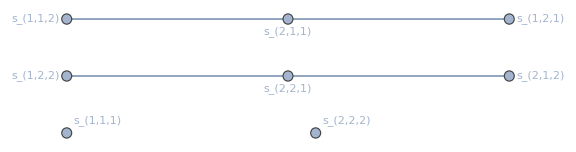

```mathematica
graphgroebner[vars3,3,ngb3]
```

```mathematica
Map[Length[VertexList[#]]&,ConnectedGraphComponents[graphgroebner[vars3,3,ngb3]]]
```

{3,3,1,1}

```mathematica
shp[{1,1},{2}]
```

{{1,1,2},{1,2,1},{2,1,1}}

```mathematica
shp[{1},{2,2}]
```

{{1,2,2},{2,1,2},{2,2,1}}

```mathematica
sols3new=First[Solve[eqs3/.sols2,vars3]]
```

Solve::svars: Equations may not give solutions for all "solve" variables.

{s_(1,1,1)→s_1^3/6,s_(1,2,1)→s_1 s_(1,2)-2 s_(1,1,2),s_(2,1,1)→1/2 (s_1^2 s_2-2 s_1 s_(1,2))+s_(1,1,2),s_(2,1,2)→s_2 s_(1,2)-2 s_(1,2,2),s_(2,2,1)→1/2 (s_1 s_2^2-2 s_2 s_(1,2))+s_(1,2,2),s_(2,2,2)→s_2^3/6}

```mathematica
sols3=Join[sols2,sols3new];
```

```mathematica
fund3=Union[Flatten[Map[Variables[Last[Apply[List,#]]]&,sols3]]]
```

{s_1,s_2,s_(1,2),s_(1,1,2),s_(1,2,2)}

#### Level 4

```mathematica
vars4=Flatten[Table[sind[{i,j,k,l}],
{i,1,2},{j,1,2},{k,1,2},{l,1,2}]];
```

```mathematica
eqs4s13=shuffles[vars1,vars3];
```

```mathematica
sols4news13=First[Solve[eqs4s13/.sols3,vars4]];
```

Solve::svars: Equations may not give solutions for all "solve" variables.

```mathematica
Length[sols4news13]
```

12

```mathematica
eqs4s22=shuffles[vars2,vars2];
```

```mathematica
Timing[ngb4=netgroebner[Join[shufflespol[vars1,vars3],shufflespol[vars2,vars2]],vars4]]
```

{0.045246,{-s_(2,2)^2+6 s_(2,2,2,2),-s_2 s_(2,2,1)+s_(2,2,1,2)+3 s_(2,2,2,1),-s_(2,1) s_(2,2)+2 s_2 s_(2,2,1)+s_(2,1,2,2)-3 s_(2,2,2,1),-s_(2,1)^2+2 s_(2,1,2,1)+4 s_(2,2,1,1),s_(2,1)^2-2 s_2 s_(2,1,1)+2 s_(2,1,1,2),-s_(1,2) s_(2,2)+2 s_(2,1) s_(2,2)-3 s_2 s_(2,2,1)+3 s_(1,2,2,2)+3 s_(2,2,2,1),s_(2,1)^2-2 s_1 s_(2,2,1)+2 s_(1,2,2,1),-2 s_(1,2) s_(2,1)-3 s_(2,1)^2+4 s_2 s_(2,1,1)+4 s_1 s_(2,2,1)+2 s_(1,2,1,2)-4 s_(2,2,1,1),-s_1 s_(2,1,1)+s_(1,2,1,1)+3 s_(2,1,1,1),-s_(1,2)^2+2 s_(1,2) s_(2,1)+3 s_(2,1)^2-4 s_2 s_(2,1,1)-4 s_1 s_(2,2,1)+4 s_(1,1,2,2)+4 s_(2,2,1,1),-s_(1,1) s_(2,1)+2 s_1 s_(2,1,1)+s_(1,1,2,1)-3 s_(2,1,1,1),-s_(1,1) s_(1,2)+2 s_(1,1) s_(2,1)-3 s_1 s_(2,1,1)+3 s_(1,1,1,2)+3 s_(2,1,1,1),-s_(1,1)^2+6 s_(1,1,1,1)}}

```mathematica
TableForm[ngb4]
```

-s_(2,2)^2+6 s_(2,2,2,2)
-s_2 s_(2,2,1)+s_(2,2,1,2)+3 s_(2,2,2,1)
-s_(2,1) s_(2,2)+2 s_2 s_(2,2,1)+s_(2,1,2,2)-3 s_(2,2,2,1)
-s_(2,1)^2+2 s_(2,1,2,1)+4 s_(2,2,1,1)
s_(2,1)^2-2 s_2 s_(2,1,1)+2 s_(2,1,1,2)
-s_(1,2) s_(2,2)+2 s_(2,1) s_(2,2)-3 s_2 s_(2,2,1)+3 s_(1,2,2,2)+3 s_(2,2,2,1)
s_(2,1)^2-2 s_1 s_(2,2,1)+2 s_(1,2,2,1)
-2 s_(1,2) s_(2,1)-3 s_(2,1)^2+4 s_2 s_(2,1,1)+4 s_1 s_(2,2,1)+2 s_(1,2,1,2)-4 s_(2,2,1,1)
-s_1 s_(2,1,1)+s_(1,2,1,1)+3 s_(2,1,1,1)
-s_(1,2)^2+2 s_(1,2) s_(2,1)+3 s_(2,1)^2-4 s_2 s_(2,1,1)-4 s_1 s_(2,2,1)+4 s_(1,1,2,2)+4 s_(2,2,1,1)
-s_(1,1) s_(2,1)+2 s_1 s_(2,1,1)+s_(1,1,2,1)-3 s_(2,1,1,1)
-s_(1,1) s_(1,2)+2 s_(1,1) s_(2,1)-3 s_1 s_(2,1,1)+3 s_(1,1,1,2)+3 s_(2,1,1,1)
-s_(1,1)^2+6 s_(1,1,1,1)

```mathematica
Length[ngb4]
```

13

```mathematica
Map[pickvars[#,4]&,ngb4]
```

{{s_(2,2,2,2)},{s_(2,2,1,2),s_(2,2,2,1)},{s_(2,1,2,2),s_(2,2,2,1)},{s_(2,1,2,1),s_(2,2,1,1)},{s_(2,1,1,2)},{s_(1,2,2,2),s_(2,2,2,1)},{s_(1,2,2,1)},{s_(1,2,1,2),s_(2,2,1,1)},{s_(1,2,1,1),s_(2,1,1,1)},{s_(1,1,2,2),s_(2,2,1,1)},{s_(1,1,2,1),s_(2,1,1,1)},{s_(1,1,1,2),s_(2,1,1,1)},{s_(1,1,1,1)}}

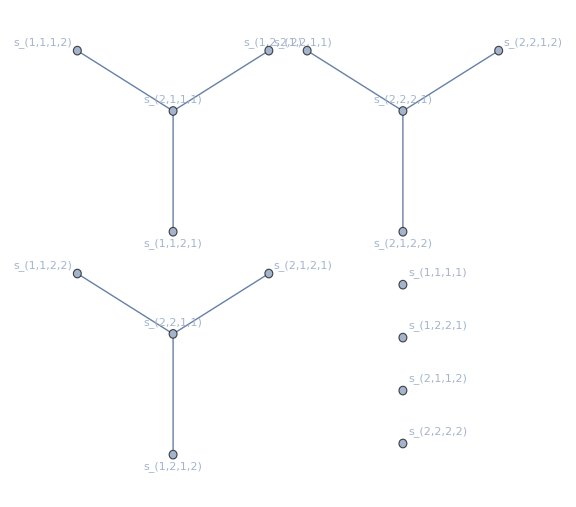

```mathematica
graphgroebner[vars4,4,ngb4]
```

```mathematica
Map[Length[VertexList[#]]&,ConnectedGraphComponents[graphgroebner[vars4,4,ngb4]]]
```

{4,4,4,1,1,1,1}

```mathematica
shp[{1,1,1},{2}]
```

{{1,1,1,2},{1,1,2,1},{1,2,1,1},{2,1,1,1}}

```mathematica
shp[{1,1},{2,2}]
```

{{1,1,2,2},{1,2,1,2},{1,2,2,1},{2,1,1,2},{2,1,2,1},{2,2,1,1}}

```mathematica
shp[{1},{2,2,2}]
```

{{1,2,2,2},{2,1,2,2},{2,2,1,2},{2,2,2,1}}

```mathematica
sols4news22=First[Solve[eqs4s22/.Join[sols3,sols4news13],vars4]];
```

Solve::svars: Equations may not give solutions for all "solve" variables.

```mathematica
Length[sols4news22]
```

1

```mathematica
sols4=Join[sols3,sols4news13/.sols4news22,sols4news22];
```

```mathematica
fund4=Union[Flatten[Map[Variables[Last[Apply[List,#]]]&,sols4]]]
```

{s_1,s_2,s_(1,2),s_(1,1,2),s_(1,2,2),s_(1,1,1,2),s_(1,1,2,2),s_(1,2,2,2)}

#### Level 5

```mathematica
vars5=Flatten[Table[sind[{i,j,k,l,m}],
{i,1,2},{j,1,2},{k,1,2},{l,1,2},{m,1,2}]];
```

```mathematica
eqs5s14=shuffles[vars1,vars4];
```

```mathematica
sols5news14=First[Solve[eqs5s14/.sols4,vars5]];
```

Solve::svars: Equations may not give solutions for all "solve" variables.

```mathematica
Length[sols5news14]
```

24

```mathematica
eqs5s23=shuffles[vars2,vars3];
```

```mathematica
Timing[ngb5=netgroebner[Join[shufflespol[vars1,vars4],shufflespol[vars2,vars3]],vars5]]
```

{8.27685,{-s_(2,2) s_(2,2,2)+10 s_(2,2,2,2,2),-s_2 s_(2,2,2,1)+s_(2,2,2,1,2)+4 s_(2,2,2,2,1),-s_(2,2) s_(2,2,1)+3 s_2 s_(2,2,2,1)+s_(2,2,1,2,2)-6 s_(2,2,2,2,1),-s_2 s_(2,2,1,1)+s_(2,2,1,1,2)+s_(2,2,1,2,1)+3 s_(2,2,2,1,1),2 s_(2,2) s_(2,2,1)-s_(2,1) s_(2,2,2)-3 s_2 s_(2,2,2,1)+s_(2,1,2,2,2)+4 s_(2,2,2,2,1),-s_(2,1) s_(2,2,1)+s_(2,1,2,2,1)+3 s_(2,2,1,2,1)+6 s_(2,2,2,1,1),-s_(2,1) s_(2,1,2)+2 s_(2,1) s_(2,2,1)+4 s_2 s_(2,2,1,1)+2 s_(2,1,2,1,2)-8 s_(2,2,1,2,1)-24 s_(2,2,2,1,1),-2 s_(2,2) s_(2,1,1)+s_(2,1) s_(2,1,2)+2 s_(2,1,1,2,2)+2 s_(2,2,1,2,1)+6 s_(2,2,2,1,1),-s_(2,1) s_(2,1,1)+s_(2,1,1,2,1)+3 s_(2,1,2,1,1)+6 s_(2,2,1,1,1),s_(2,1) s_(2,1,1)-s_2 s_(2,1,1,1)+s_(2,1,1,1,2)-2 s_(2,1,2,1,1)-4 s_(2,2,1,1,1),-4 s_(2,2) s_(2,2,1)-s_(1,2) s_(2,2,2)+3 s_(2,1) s_(2,2,2)+4 s_2 s_(2,2,2,1)+4 s_(1,2,2,2,2)-4 s_(2,2,2,2,1),s_(2,1) s_(2,2,1)-s_1 s_(2,2,2,1)+s_(1,2,2,2,1)-2 s_(2,2,1,2,1)-4 s_(2,2,2,1,1),s_(2,1) s_(2,1,2)-2 s_(1,2) s_(2,2,1)-4 s_(2,1) s_(2,2,1)+6 s_1 s_(2,2,2,1)+2 s_(1,2,2,1,2)+6 s_(2,2,1,2,1)+12 s_(2,2,2,1,1),-s_1 s_(2,2,1,1)+s_(1,2,2,1,1)+s_(2,1,2,1,1)+3 s_(2,2,1,1,1),4 s_(2,2) s_(2,1,1)-s_(1,2) s_(2,1,2)-2 s_(2,1) s_(2,1,2)+2 s_(1,2) s_(2,2,1)+2 s_(2,1) s_(2,2,1)-4 s_2 s_(2,2,1,1)-6 s_1 s_(2,2,2,1)+2 s_(1,2,1,2,2)-2 s_(2,2,1,2,1),-s_(2,1) s_(1,2,1)+2 s_(2,1) s_(2,1,1)+4 s_1 s_(2,2,1,1)+2 s_(1,2,1,2,1)-8 s_(2,1,2,1,1)-24 s_(2,2,1,1,1),s_(2,1) s_(1,2,1)-2 s_(1,2) s_(2,1,1)-4 s_(2,1) s_(2,1,1)+6 s_2 s_(2,1,1,1)+2 s_(1,2,1,1,2)+6 s_(2,1,2,1,1)+12 s_(2,2,1,1,1),-s_1 s_(2,1,1,1)+s_(1,2,1,1,1)+4 s_(2,1,1,1,1),-2 s_(1,2) s_(1,2,2)-12 s_(2,2) s_(2,1,1)+3 s_(1,2) s_(2,1,2)+5 s_(2,1) s_(2,1,2)-4 s_(1,2) s_(2,2,1)-2 s_(2,1) s_(2,2,1)+12 s_2 s_(2,2,1,1)+12 s_1 s_(2,2,2,1)+12 s_(1,1,2,2,2)-12 s_(2,2,2,1,1),s_(2,1) s_(1,2,1)-2 s_(1,1) s_(2,2,1)+2 s_(1,1,2,2,1)+2 s_(2,1,2,1,1)+6 s_(2,2,1,1,1),-s_(1,2) s_(1,2,1)-2 s_(2,1) s_(1,2,1)+2 s_(1,2) s_(2,1,1)+2 s_(2,1) s_(2,1,1)+4 s_(1,1) s_(2,2,1)-6 s_2 s_(2,1,1,1)-4 s_1 s_(2,2,1,1)+2 s_(1,1,2,1,2)-2 s_(2,1,2,1,1),-s_(1,1) s_(2,1,1)+3 s_1 s_(2,1,1,1)+s_(1,1,2,1,1)-6 s_(2,1,1,1,1),-2 s_(1,2) s_(1,1,2)+3 s_(1,2) s_(1,2,1)+5 s_(2,1) s_(1,2,1)-4 s_(1,2) s_(2,1,1)-2 s_(2,1) s_(2,1,1)-12 s_(1,1) s_(2,2,1)+12 s_2 s_(2,1,1,1)+12 s_1 s_(2,2,1,1)+12 s_(1,1,1,2,2)-12 s_(2,2,1,1,1),-s_(2,1) s_(1,1,1)+2 s_(1,1) s_(2,1,1)-3 s_1 s_(2,1,1,1)+s_(1,1,1,2,1)+4 s_(2,1,1,1,1),-s_(1,2) s_(1,1,1)+3 s_(2,1) s_(1,1,1)-4 s_(1,1) s_(2,1,1)+4 s_1 s_(2,1,1,1)+4 s_(1,1,1,1,2)-4 s_(2,1,1,1,1),-s_(1,1) s_(1,1,1)+10 s_(1,1,1,1,1)}}

```mathematica
TableForm[ngb5]
```

-s_(2,2) s_(2,2,2)+10 s_(2,2,2,2,2)
-s_2 s_(2,2,2,1)+s_(2,2,2,1,2)+4 s_(2,2,2,2,1)
-s_(2,2) s_(2,2,1)+3 s_2 s_(2,2,2,1)+s_(2,2,1,2,2)-6 s_(2,2,2,2,1)
-s_2 s_(2,2,1,1)+s_(2,2,1,1,2)+s_(2,2,1,2,1)+3 s_(2,2,2,1,1)
2 s_(2,2) s_(2,2,1)-s_(2,1) s_(2,2,2)-3 s_2 s_(2,2,2,1)+s_(2,1,2,2,2)+4 s_(2,2,2,2,1)
-s_(2,1) s_(2,2,1)+s_(2,1,2,2,1)+3 s_(2,2,1,2,1)+6 s_(2,2,2,1,1)
-s_(2,1) s_(2,1,2)+2 s_(2,1) s_(2,2,1)+4 s_2 s_(2,2,1,1)+2 s_(2,1,2,1,2)-8 s_(2,2,1,2,1)-24 s_(2,2,2,1,1)
-2 s_(2,2) s_(2,1,1)+s_(2,1) s_(2,1,2)+2 s_(2,1,1,2,2)+2 s_(2,2,1,2,1)+6 s_(2,2,2,1,1)
-s_(2,1) s_(2,1,1)+s_(2,1,1,2,1)+3 s_(2,1,2,1,1)+6 s_(2,2,1,1,1)
s_(2,1) s_(2,1,1)-s_2 s_(2,1,1,1)+s_(2,1,1,1,2)-2 s_(2,1,2,1,1)-4 s_(2,2,1,1,1)
-4 s_(2,2) s_(2,2,1)-s_(1,2) s_(2,2,2)+3 s_(2,1) s_(2,2,2)+4 s_2 s_(2,2,2,1)+4 s_(1,2,2,2,2)-4 s_(2,2,2,2,1)
s_(2,1) s_(2,2,1)-s_1 s_(2,2,2,1)+s_(1,2,2,2,1)-2 s_(2,2,1,2,1)-4 s_(2,2,2,1,1)
s_(2,1) s_(2,1,2)-2 s_(1,2) s_(2,2,1)-4 s_(2,1) s_(2,2,1)+6 s_1 s_(2,2,2,1)+2 s_(1,2,2,1,2)+6 s_(2,2,1,2,1)+12 s_(2,2,2,1,1)
-s_1 s_(2,2,1,1)+s_(1,2,2,1,1)+s_(2,1,2,1,1)+3 s_(2,2,1,1,1)
4 s_(2,2) s_(2,1,1)-s_(1,2) s_(2,1,2)-2 s_(2,1) s_(2,1,2)+2 s_(1,2) s_(2,2,1)+2 s_(2,1) s_(2,2,1)-4 s_2 s_(2,2,1,1)-6 s_1 s_(2,2,2,1)+2 s_(1,2,1,2,2)-2 s_(2,2,1,2,1)
-s_(2,1) s_(1,2,1)+2 s_(2,1) s_(2,1,1)+4 s_1 s_(2,2,1,1)+2 s_(1,2,1,2,1)-8 s_(2,1,2,1,1)-24 s_(2,2,1,1,1)
s_(2,1) s_(1,2,1)-2 s_(1,2) s_(2,1,1)-4 s_(2,1) s_(2,1,1)+6 s_2 s_(2,1,1,1)+2 s_(1,2,1,1,2)+6 s_(2,1,2,1,1)+12 s_(2,2,1,1,1)
-s_1 s_(2,1,1,1)+s_(1,2,1,1,1)+4 s_(2,1,1,1,1)
-2 s_(1,2) s_(1,2,2)-12 s_(2,2) s_(2,1,1)+3 s_(1,2) s_(2,1,2)+5 s_(2,1) s_(2,1,2)-4 s_(1,2) s_(2,2,1)-2 s_(2,1) s_(2,2,1)+12 s_2 s_(2,2,1,1)+12 s_1 s_(2,2,2,1)+12 s_(1,1,2,2,2)-12 s_(2,2,2,1,1)
s_(2,1) s_(1,2,1)-2 s_(1,1) s_(2,2,1)+2 s_(1,1,2,2,1)+2 s_(2,1,2,1,1)+6 s_(2,2,1,1,1)
-s_(1,2) s_(1,2,1)-2 s_(2,1) s_(1,2,1)+2 s_(1,2) s_(2,1,1)+2 s_(2,1) s_(2,1,1)+4 s_(1,1) s_(2,2,1)-6 s_2 s_(2,1,1,1)-4 s_1 s_(2,2,1,1)+2 s_(1,1,2,1,2)-2 s_(2,1,2,1,1)
-s_(1,1) s_(2,1,1)+3 s_1 s_(2,1,1,1)+s_(1,1,2,1,1)-6 s_(2,1,1,1,1)
-2 s_(1,2) s_(1,1,2)+3 s_(1,2) s_(1,2,1)+5 s_(2,1) s_(1,2,1)-4 s_(1,2) s_(2,1,1)-2 s_(2,1) s_(2,1,1)-12 s_(1,1) s_(2,2,1)+12 s_2 s_(2,1,1,1)+12 s_1 s_(2,2,1,1)+12 s_(1,1,1,2,2)-12 s_(2,2,1,1,1)
-s_(2,1) s_(1,1,1)+2 s_(1,1) s_(2,1,1)-3 s_1 s_(2,1,1,1)+s_(1,1,1,2,1)+4 s_(2,1,1,1,1)
-s_(1,2) s_(1,1,1)+3 s_(2,1) s_(1,1,1)-4 s_(1,1) s_(2,1,1)+4 s_1 s_(2,1,1,1)+4 s_(1,1,1,1,2)-4 s_(2,1,1,1,1)
-s_(1,1) s_(1,1,1)+10 s_(1,1,1,1,1)

```mathematica
Map[pickvars[#,5]&,ngb5]
```

{{s_(2,2,2,2,2)},{s_(2,2,2,1,2),s_(2,2,2,2,1)},{s_(2,2,1,2,2),s_(2,2,2,2,1)},{s_(2,2,1,1,2),s_(2,2,1,2,1),s_(2,2,2,1,1)},{s_(2,1,2,2,2),s_(2,2,2,2,1)},{s_(2,1,2,2,1),s_(2,2,1,2,1),s_(2,2,2,1,1)},{s_(2,1,2,1,2),s_(2,2,1,2,1),s_(2,2,2,1,1)},{s_(2,1,1,2,2),s_(2,2,1,2,1),s_(2,2,2,1,1)},{s_(2,1,1,2,1),s_(2,1,2,1,1),s_(2,2,1,1,1)},{s_(2,1,1,1,2),s_(2,1,2,1,1),s_(2,2,1,1,1)},{s_(1,2,2,2,2),s_(2,2,2,2,1)},{s_(1,2,2,2,1),s_(2,2,1,2,1),s_(2,2,2,1,1)},{s_(1,2,2,1,2),s_(2,2,1,2,1),s_(2,2,2,1,1)},{s_(1,2,2,1,1),s_(2,1,2,1,1),s_(2,2,1,1,1)},{s_(1,2,1,2,2),s_(2,2,1,2,1)},{s_(1,2,1,2,1),s_(2,1,2,1,1),s_(2,2,1,1,1)},{s_(1,2,1,1,2),s_(2,1,2,1,1),s_(2,2,1,1,1)},{s_(1,2,1,1,1),s_(2,1,1,1,1)},{s_(1,1,2,2,2),s_(2,2,2,1,1)},{s_(1,1,2,2,1),s_(2,1,2,1,1),s_(2,2,1,1,1)},{s_(1,1,2,1,2),s_(2,1,2,1,1)},{s_(1,1,2,1,1),s_(2,1,1,1,1)},{s_(1,1,1,2,2),s_(2,2,1,1,1)},{s_(1,1,1,2,1),s_(2,1,1,1,1)},{s_(1,1,1,1,2),s_(2,1,1,1,1)},{s_(1,1,1,1,1)}}

```mathematica
groups5=Select[Map[pickvars[#,5]&,ngb5],(Length[#]>1)&]
```

{{s_(2,2,2,1,2),s_(2,2,2,2,1)},{s_(2,2,1,2,2),s_(2,2,2,2,1)},{s_(2,2,1,1,2),s_(2,2,1,2,1),s_(2,2,2,1,1)},{s_(2,1,2,2,2),s_(2,2,2,2,1)},{s_(2,1,2,2,1),s_(2,2,1,2,1),s_(2,2,2,1,1)},{s_(2,1,2,1,2),s_(2,2,1,2,1),s_(2,2,2,1,1)},{s_(2,1,1,2,2),s_(2,2,1,2,1),s_(2,2,2,1,1)},{s_(2,1,1,2,1),s_(2,1,2,1,1),s_(2,2,1,1,1)},{s_(2,1,1,1,2),s_(2,1,2,1,1),s_(2,2,1,1,1)},{s_(1,2,2,2,2),s_(2,2,2,2,1)},{s_(1,2,2,2,1),s_(2,2,1,2,1),s_(2,2,2,1,1)},{s_(1,2,2,1,2),s_(2,2,1,2,1),s_(2,2,2,1,1)},{s_(1,2,2,1,1),s_(2,1,2,1,1),s_(2,2,1,1,1)},{s_(1,2,1,2,2),s_(2,2,1,2,1)},{s_(1,2,1,2,1),s_(2,1,2,1,1),s_(2,2,1,1,1)},{s_(1,2,1,1,2),s_(2,1,2,1,1),s_(2,2,1,1,1)},{s_(1,2,1,1,1),s_(2,1,1,1,1)},{s_(1,1,2,2,2),s_(2,2,2,1,1)},{s_(1,1,2,2,1),s_(2,1,2,1,1),s_(2,2,1,1,1)},{s_(1,1,2,1,2),s_(2,1,2,1,1)},{s_(1,1,2,1,1),s_(2,1,1,1,1)},{s_(1,1,1,2,2),s_(2,2,1,1,1)},{s_(1,1,1,2,1),s_(2,1,1,1,1)},{s_(1,1,1,1,2),s_(2,1,1,1,1)}}

```mathematica
Select[Map[pickvars[#,5]&,ngb5],(Length[#]==2)&]
```

{{s_(2,2,2,1,2),s_(2,2,2,2,1)},{s_(2,2,1,2,2),s_(2,2,2,2,1)},{s_(2,1,2,2,2),s_(2,2,2,2,1)},{s_(1,2,2,2,2),s_(2,2,2,2,1)},{s_(1,2,1,2,2),s_(2,2,1,2,1)},{s_(1,2,1,1,1),s_(2,1,1,1,1)},{s_(1,1,2,2,2),s_(2,2,2,1,1)},{s_(1,1,2,1,2),s_(2,1,2,1,1)},{s_(1,1,2,1,1),s_(2,1,1,1,1)},{s_(1,1,1,2,2),s_(2,2,1,1,1)},{s_(1,1,1,2,1),s_(2,1,1,1,1)},{s_(1,1,1,1,2),s_(2,1,1,1,1)}}

```mathematica
Select[Map[pickvars[#,5]&,ngb5],(Length[#]==3)&]
```

{{s_(2,2,1,1,2),s_(2,2,1,2,1),s_(2,2,2,1,1)},{s_(2,1,2,2,1),s_(2,2,1,2,1),s_(2,2,2,1,1)},{s_(2,1,2,1,2),s_(2,2,1,2,1),s_(2,2,2,1,1)},{s_(2,1,1,2,2),s_(2,2,1,2,1),s_(2,2,2,1,1)},{s_(2,1,1,2,1),s_(2,1,2,1,1),s_(2,2,1,1,1)},{s_(2,1,1,1,2),s_(2,1,2,1,1),s_(2,2,1,1,1)},{s_(1,2,2,2,1),s_(2,2,1,2,1),s_(2,2,2,1,1)},{s_(1,2,2,1,2),s_(2,2,1,2,1),s_(2,2,2,1,1)},{s_(1,2,2,1,1),s_(2,1,2,1,1),s_(2,2,1,1,1)},{s_(1,2,1,2,1),s_(2,1,2,1,1),s_(2,2,1,1,1)},{s_(1,2,1,1,2),s_(2,1,2,1,1),s_(2,2,1,1,1)},{s_(1,1,2,2,1),s_(2,1,2,1,1),s_(2,2,1,1,1)}}

```mathematica
pairs5=Union[Flatten[Map[Subsets[#,{2}]&,groups5],1]]
```

{{s_(1,1,1,1,2),s_(2,1,1,1,1)},{s_(1,1,1,2,1),s_(2,1,1,1,1)},{s_(1,1,1,2,2),s_(2,2,1,1,1)},{s_(1,1,2,1,1),s_(2,1,1,1,1)},{s_(1,1,2,1,2),s_(2,1,2,1,1)},{s_(1,1,2,2,1),s_(2,1,2,1,1)},{s_(1,1,2,2,1),s_(2,2,1,1,1)},{s_(1,1,2,2,2),s_(2,2,2,1,1)},{s_(1,2,1,1,1),s_(2,1,1,1,1)},{s_(1,2,1,1,2),s_(2,1,2,1,1)},{s_(1,2,1,1,2),s_(2,2,1,1,1)},{s_(1,2,1,2,1),s_(2,1,2,1,1)},{s_(1,2,1,2,1),s_(2,2,1,1,1)},{s_(1,2,1,2,2),s_(2,2,1,2,1)},{s_(1,2,2,1,1),s_(2,1,2,1,1)},{s_(1,2,2,1,1),s_(2,2,1,1,1)},{s_(1,2,2,1,2),s_(2,2,1,2,1)},{s_(1,2,2,1,2),s_(2,2,2,1,1)},{s_(1,2,2,2,1),s_(2,2,1,2,1)},{s_(1,2,2,2,1),s_(2,2,2,1,1)},{s_(1,2,2,2,2),s_(2,2,2,2,1)},{s_(2,1,1,1,2),s_(2,1,2,1,1)},{s_(2,1,1,1,2),s_(2,2,1,1,1)},{s_(2,1,1,2,1),s_(2,1,2,1,1)},{s_(2,1,1,2,1),s_(2,2,1,1,1)},{s_(2,1,1,2,2),s_(2,2,1,2,1)},{s_(2,1,1,2,2),s_(2,2,2,1,1)},{s_(2,1,2,1,1),s_(2,2,1,1,1)},{s_(2,1,2,1,2),s_(2,2,1,2,1)},{s_(2,1,2,1,2),s_(2,2,2,1,1)},{s_(2,1,2,2,1),s_(2,2,1,2,1)},{s_(2,1,2,2,1),s_(2,2,2,1,1)},{s_(2,1,2,2,2),s_(2,2,2,2,1)},{s_(2,2,1,1,2),s_(2,2,1,2,1)},{s_(2,2,1,1,2),s_(2,2,2,1,1)},{s_(2,2,1,2,1),s_(2,2,2,1,1)},{s_(2,2,1,2,2),s_(2,2,2,2,1)},{s_(2,2,2,1,2),s_(2,2,2,2,1)}}

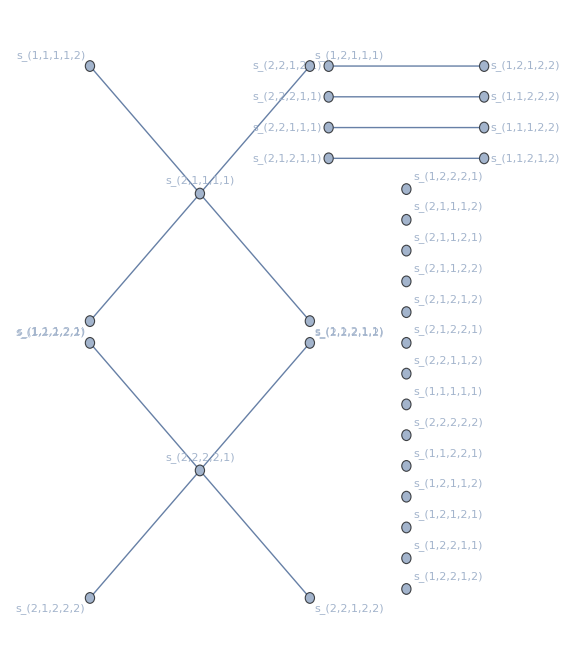

```mathematica
graphgroebner2[vars5,5,ngb5]
```

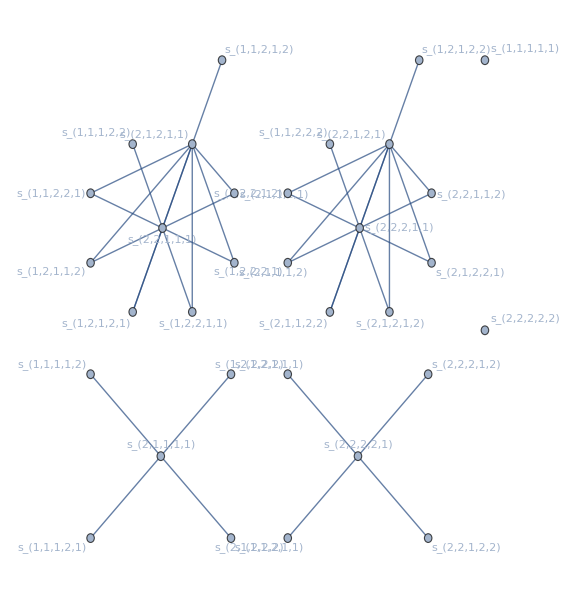

```mathematica
graphgroebner[vars5,5,ngb5]
```

```mathematica
Grap
```

```mathematica
ArrayPlot[adjgroebner[vars5,5,ngb5],Mesh->True]
```

-Graphics-

```mathematica
Transpose[{vars5,Map[Total,adjgroebner[vars5,5,ngb5]]}]
```

{{s_(1,1,1,1,1),0},{s_(1,1,1,1,2),1},{s_(1,1,1,2,1),1},{s_(1,1,1,2,2),1},{s_(1,1,2,1,1),1},{s_(1,1,2,1,2),1},{s_(1,1,2,2,1),2},{s_(1,1,2,2,2),1},{s_(1,2,1,1,1),1},{s_(1,2,1,1,2),2},{s_(1,2,1,2,1),2},{s_(1,2,1,2,2),1},{s_(1,2,2,1,1),2},{s_(1,2,2,1,2),2},{s_(1,2,2,2,1),2},{s_(1,2,2,2,2),1},{s_(2,1,1,1,1),4},{s_(2,1,1,1,2),2},{s_(2,1,1,2,1),2},{s_(2,1,1,2,2),2},{s_(2,1,2,1,1),8},{s_(2,1,2,1,2),2},{s_(2,1,2,2,1),2},{s_(2,1,2,2,2),1},{s_(2,2,1,1,1),8},{s_(2,2,1,1,2),2},{s_(2,2,1,2,1),8},{s_(2,2,1,2,2),1},{s_(2,2,2,1,1),8},{s_(2,2,2,1,2),1},{s_(2,2,2,2,1),4},{s_(2,2,2,2,2),0}}

```mathematica
Transpose[{vars5,VertexDegree[graphgroebner[vars5,5,ngb5]]}]
```

{{s_(1,1,1,1,1),0},{s_(1,1,1,1,2),1},{s_(1,1,1,2,1),1},{s_(1,1,1,2,2),1},{s_(1,1,2,1,1),1},{s_(1,1,2,1,2),1},{s_(1,1,2,2,1),2},{s_(1,1,2,2,2),1},{s_(1,2,1,1,1),1},{s_(1,2,1,1,2),2},{s_(1,2,1,2,1),2},{s_(1,2,1,2,2),1},{s_(1,2,2,1,1),2},{s_(1,2,2,1,2),2},{s_(1,2,2,2,1),2},{s_(1,2,2,2,2),1},{s_(2,1,1,1,1),4},{s_(2,1,1,1,2),2},{s_(2,1,1,2,1),2},{s_(2,1,1,2,2),2},{s_(2,1,2,1,1),8},{s_(2,1,2,1,2),2},{s_(2,1,2,2,1),2},{s_(2,1,2,2,2),1},{s_(2,2,1,1,1),8},{s_(2,2,1,1,2),2},{s_(2,2,1,2,1),8},{s_(2,2,1,2,2),1},{s_(2,2,2,1,1),8},{s_(2,2,2,1,2),1},{s_(2,2,2,2,1),4},{s_(2,2,2,2,2),0}}

```mathematica
Map[Length[VertexList[#]]&,ConnectedGraphComponents[graphgroebner[vars5,5,ngb5]]]
```

{10,10,5,5,1,1}

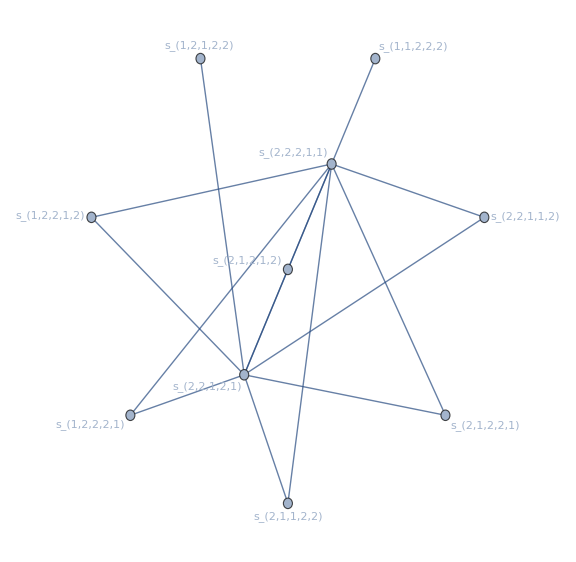

```mathematica
ConnectedGraphComponents[graphgroebner[vars5,5,ngb5]][[1]]
```

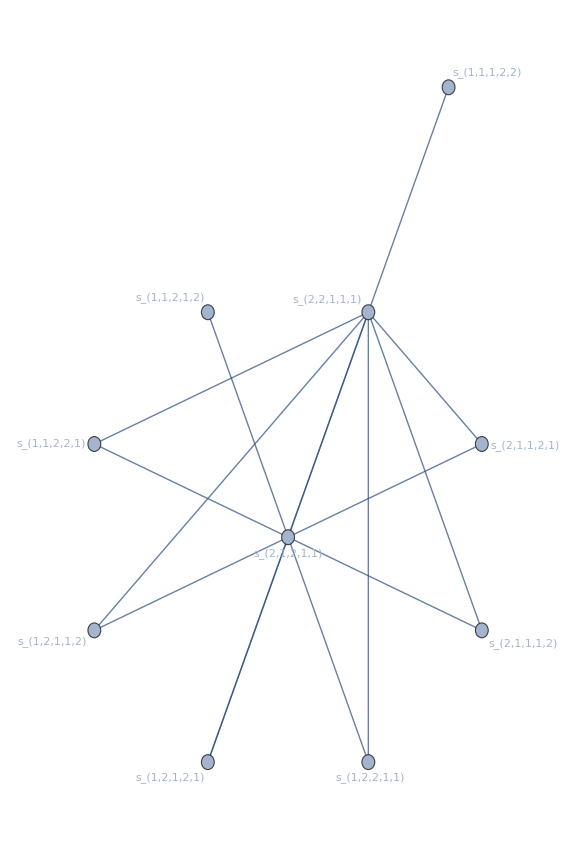

```mathematica
ConnectedGraphComponents[graphgroebner[vars5,5,ngb5]][[2]]
```

```mathematica
sols5news23=First[Solve[eqs5s23/.Join[sols4,sols5news14],vars5]];
```

Solve::svars: Equations may not give solutions for all "solve" variables.

```mathematica
Length[sols5news23]
```

2

```mathematica
sols5=Join[sols4,sols5news14/.sols5news23,sols5news23];
```

```mathematica
fund5=Union[Flatten[Map[Variables[Last[Apply[List,#]]]&,sols5]]]
```

{s_1,s_2,s_(1,2),s_(1,1,2),s_(1,2,2),s_(1,1,1,2),s_(1,1,2,2),s_(1,2,2,2),s_(1,1,1,1,2),s_(1,1,1,2,2),s_(1,1,2,1,2),s_(1,1,2,2,2),s_(1,2,1,2,2),s_(1,2,2,2,2)}

#### Level 6

```mathematica
vars6=Flatten[Table[sind[{i,j,k,l,m,n}],
{i,1,2},{j,1,2},{k,1,2},{l,1,2},{m,1,2},{n,1,2}]];
```

```mathematica
eqs6s15=shuffles[vars1,vars5];
```

```mathematica
ArrayPlot[Last[Normal[CoefficientArrays[Map[(First[#]-Last[#]==0)&,DeleteDuplicates[Transpose[Apply[List,eqs6s15]]]],vars6]]]]
```

-Graphics-

```mathematica
sols6news15=First[Solve[eqs6s15/.sols5,vars6]];
```

Solve::svars: Equations may not give solutions for all "solve" variables.

```mathematica
Length[sols6news15]
```

48

```mathematica
eqs6s24=shuffles[vars2,vars4];
```

```mathematica
ArrayPlot[Last[Normal[CoefficientArrays[Map[(First[#]-Last[#]==0)&,DeleteDuplicates[Transpose[Apply[List,eqs6s24]]]],vars6]]]]
```

-Graphics-

```mathematica
sols6news24=First[Solve[eqs6s24/.Join[sols5,sols6news15],vars6]];
```

Solve::svars: Equations may not give solutions for all "solve" variables.

```mathematica
Length[sols6news24]
```

4

```mathematica
eqs6s33=shuffles[vars3,vars3];
```

```mathematica
ArrayPlot[Last[Normal[CoefficientArrays[Map[(First[#]-Last[#]==0)&,DeleteDuplicates[Transpose[Apply[List,eqs6s33]]]],vars6]]]]
```

-Graphics-

```mathematica
sols6news33=First[Solve[eqs6s33/.Join[sols5,sols6news15/.sols6news24,sols6news24],vars6]];
```

Solve::svars: Equations may not give solutions for all "solve" variables.

```mathematica
Length[sols6news33]
```

3

```mathematica
{{Length[shufflespol[vars1,vars5]],Length[DeleteDuplicates[shufflespol[vars1,vars5]]]},
{Length[shufflespol[vars2,vars4]],Length[DeleteDuplicates[shufflespol[vars2,vars4]]]},
{Length[shufflespol[vars3,vars3]],Length[DeleteDuplicates[shufflespol[vars3,vars3]]]}}
```

{{64,64},{64,64},{64,36}}

```mathematica
Timing[ngb6s15=netgroebner[shufflespol[vars1,vars5],vars6];]
```

{9.41535,Null}

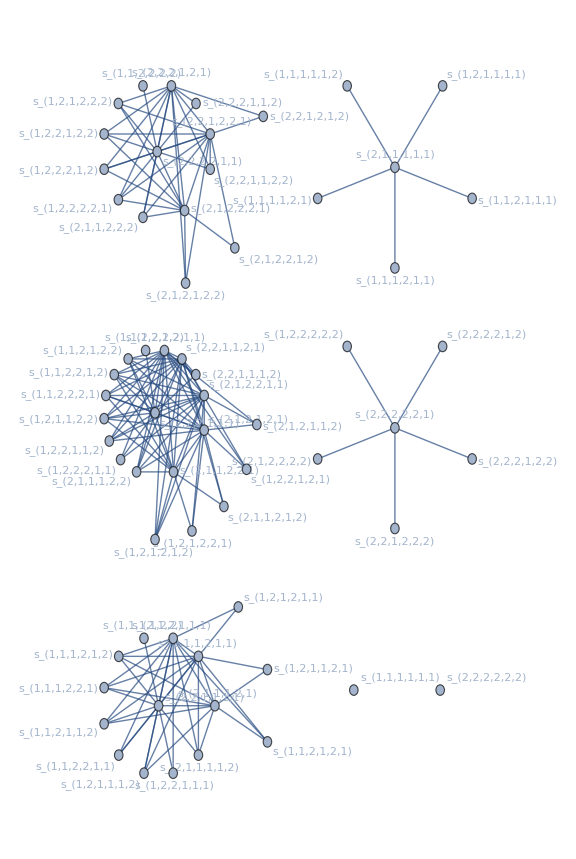

```mathematica
graphgroebner[vars6,6,ngb6s15]
```

```mathematica
Map[Length[VertexList[#]]&,ConnectedGraphComponents[graphgroebner[vars6,6,ngb6s15]]]
```

{20,15,15,6,6,1,1}

```mathematica
Timing[ngb6s24=netgroebner[shufflespol[vars2,vars4],vars6];]
```

{0.706315,Null}

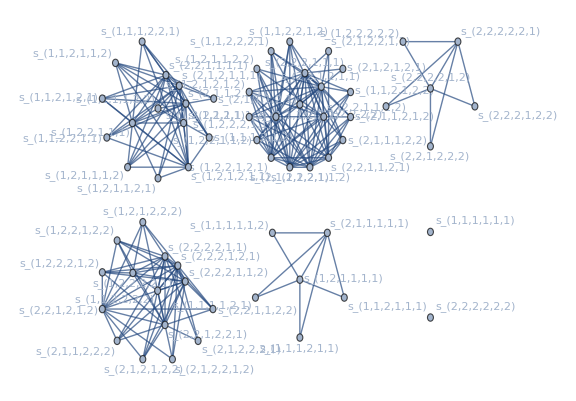

```mathematica
graphgroebner[vars6,6,ngb6s24]
```

```mathematica
Map[Length[VertexList[#]]&,ConnectedGraphComponents[graphgroebner[vars6,6,ngb6s24]]]
```

{20,15,15,6,6,1,1}

```mathematica
Timing[ngb6s33=netgroebner[DeleteDuplicates[shufflespol[vars3,vars3]],vars6];]
```

{0.025654,Null}

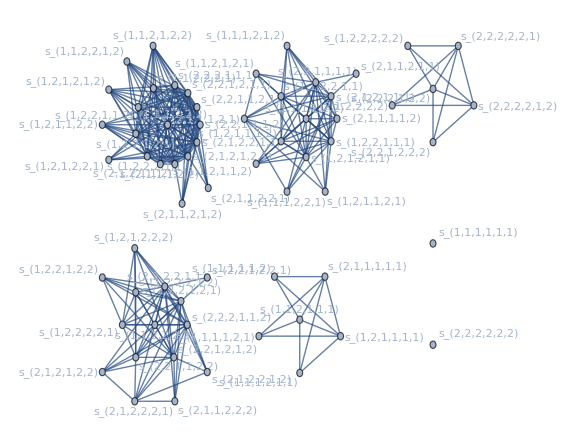

```mathematica
graphgroebner[vars6,6,ngb6s33]
```

```mathematica
Map[Length[VertexList[#]]&,ConnectedGraphComponents[graphgroebner[vars6,6,ngb6s33]]]
```

{20,15,15,6,6,1,1}

```mathematica
Timing[ngb6=netgroebner[DeleteDuplicates[Join[ngb6s15,ngb6s24,ngb6s33]],vars6]]
```

$Aborted

```mathematica
TableForm[ngb6]
```

-s_(2,2) s_(2,2,2)+10 s_(2,2,2,2,2)
-s_2 s_(2,2,2,1)+s_(2,2,2,1,2)+4 s_(2,2,2,2,1)
-s_(2,2) s_(2,2,1)+3 s_2 s_(2,2,2,1)+s_(2,2,1,2,2)-6 s_(2,2,2,2,1)
-s_2 s_(2,2,1,1)+s_(2,2,1,1,2)+s_(2,2,1,2,1)+3 s_(2,2,2,1,1)
2 s_(2,2) s_(2,2,1)-s_(2,1) s_(2,2,2)-3 s_2 s_(2,2,2,1)+s_(2,1,2,2,2)+4 s_(2,2,2,2,1)
-s_(2,1) s_(2,2,1)+s_(2,1,2,2,1)+3 s_(2,2,1,2,1)+6 s_(2,2,2,1,1)
-s_(2,1) s_(2,1,2)+2 s_(2,1) s_(2,2,1)+4 s_2 s_(2,2,1,1)+2 s_(2,1,2,1,2)-8 s_(2,2,1,2,1)-24 s_(2,2,2,1,1)
-2 s_(2,2) s_(2,1,1)+s_(2,1) s_(2,1,2)+2 s_(2,1,1,2,2)+2 s_(2,2,1,2,1)+6 s_(2,2,2,1,1)
-s_(2,1) s_(2,1,1)+s_(2,1,1,2,1)+3 s_(2,1,2,1,1)+6 s_(2,2,1,1,1)
s_(2,1) s_(2,1,1)-s_2 s_(2,1,1,1)+s_(2,1,1,1,2)-2 s_(2,1,2,1,1)-4 s_(2,2,1,1,1)
-4 s_(2,2) s_(2,2,1)-s_(1,2) s_(2,2,2)+3 s_(2,1) s_(2,2,2)+4 s_2 s_(2,2,2,1)+4 s_(1,2,2,2,2)-4 s_(2,2,2,2,1)
s_(2,1) s_(2,2,1)-s_1 s_(2,2,2,1)+s_(1,2,2,2,1)-2 s_(2,2,1,2,1)-4 s_(2,2,2,1,1)
s_(2,1) s_(2,1,2)-2 s_(1,2) s_(2,2,1)-4 s_(2,1) s_(2,2,1)+6 s_1 s_(2,2,2,1)+2 s_(1,2,2,1,2)+6 s_(2,2,1,2,1)+12 s_(2,2,2,1,1)
-s_1 s_(2,2,1,1)+s_(1,2,2,1,1)+s_(2,1,2,1,1)+3 s_(2,2,1,1,1)
4 s_(2,2) s_(2,1,1)-s_(1,2) s_(2,1,2)-2 s_(2,1) s_(2,1,2)+2 s_(1,2) s_(2,2,1)+2 s_(2,1) s_(2,2,1)-4 s_2 s_(2,2,1,1)-6 s_1 s_(2,2,2,1)+2 s_(1,2,1,2,2)-2 s_(2,2,1,2,1)
-s_(2,1) s_(1,2,1)+2 s_(2,1) s_(2,1,1)+4 s_1 s_(2,2,1,1)+2 s_(1,2,1,2,1)-8 s_(2,1,2,1,1)-24 s_(2,2,1,1,1)
s_(2,1) s_(1,2,1)-2 s_(1,2) s_(2,1,1)-4 s_(2,1) s_(2,1,1)+6 s_2 s_(2,1,1,1)+2 s_(1,2,1,1,2)+6 s_(2,1,2,1,1)+12 s_(2,2,1,1,1)
-s_1 s_(2,1,1,1)+s_(1,2,1,1,1)+4 s_(2,1,1,1,1)
-2 s_(1,2) s_(1,2,2)-12 s_(2,2) s_(2,1,1)+3 s_(1,2) s_(2,1,2)+5 s_(2,1) s_(2,1,2)-4 s_(1,2) s_(2,2,1)-2 s_(2,1) s_(2,2,1)+12 s_2 s_(2,2,1,1)+12 s_1 s_(2,2,2,1)+12 s_(1,1,2,2,2)-12 s_(2,2,2,1,1)
s_(2,1) s_(1,2,1)-2 s_(1,1) s_(2,2,1)+2 s_(1,1,2,2,1)+2 s_(2,1,2,1,1)+6 s_(2,2,1,1,1)
-s_(1,2) s_(1,2,1)-2 s_(2,1) s_(1,2,1)+2 s_(1,2) s_(2,1,1)+2 s_(2,1) s_(2,1,1)+4 s_(1,1) s_(2,2,1)-6 s_2 s_(2,1,1,1)-4 s_1 s_(2,2,1,1)+2 s_(1,1,2,1,2)-2 s_(2,1,2,1,1)
-s_(1,1) s_(2,1,1)+3 s_1 s_(2,1,1,1)+s_(1,1,2,1,1)-6 s_(2,1,1,1,1)
-2 s_(1,2) s_(1,1,2)+3 s_(1,2) s_(1,2,1)+5 s_(2,1) s_(1,2,1)-4 s_(1,2) s_(2,1,1)-2 s_(2,1) s_(2,1,1)-12 s_(1,1) s_(2,2,1)+12 s_2 s_(2,1,1,1)+12 s_1 s_(2,2,1,1)+12 s_(1,1,1,2,2)-12 s_(2,2,1,1,1)
-s_(2,1) s_(1,1,1)+2 s_(1,1) s_(2,1,1)-3 s_1 s_(2,1,1,1)+s_(1,1,1,2,1)+4 s_(2,1,1,1,1)
-s_(1,2) s_(1,1,1)+3 s_(2,1) s_(1,1,1)-4 s_(1,1) s_(2,1,1)+4 s_1 s_(2,1,1,1)+4 s_(1,1,1,1,2)-4 s_(2,1,1,1,1)
-s_(1,1) s_(1,1,1)+10 s_(1,1,1,1,1)

```mathematica
Map[pickvars[#,6]&,ngb6]
```

{{s_(2,2,2,2,2)},{s_(2,2,2,1,2),s_(2,2,2,2,1)},{s_(2,2,1,2,2),s_(2,2,2,2,1)},{s_(2,2,1,1,2),s_(2,2,1,2,1),s_(2,2,2,1,1)},{s_(2,1,2,2,2),s_(2,2,2,2,1)},{s_(2,1,2,2,1),s_(2,2,1,2,1),s_(2,2,2,1,1)},{s_(2,1,2,1,2),s_(2,2,1,2,1),s_(2,2,2,1,1)},{s_(2,1,1,2,2),s_(2,2,1,2,1),s_(2,2,2,1,1)},{s_(2,1,1,2,1),s_(2,1,2,1,1),s_(2,2,1,1,1)},{s_(2,1,1,1,2),s_(2,1,2,1,1),s_(2,2,1,1,1)},{s_(1,2,2,2,2),s_(2,2,2,2,1)},{s_(1,2,2,2,1),s_(2,2,1,2,1),s_(2,2,2,1,1)},{s_(1,2,2,1,2),s_(2,2,1,2,1),s_(2,2,2,1,1)},{s_(1,2,2,1,1),s_(2,1,2,1,1),s_(2,2,1,1,1)},{s_(1,2,1,2,2),s_(2,2,1,2,1)},{s_(1,2,1,2,1),s_(2,1,2,1,1),s_(2,2,1,1,1)},{s_(1,2,1,1,2),s_(2,1,2,1,1),s_(2,2,1,1,1)},{s_(1,2,1,1,1),s_(2,1,1,1,1)},{s_(1,1,2,2,2),s_(2,2,2,1,1)},{s_(1,1,2,2,1),s_(2,1,2,1,1),s_(2,2,1,1,1)},{s_(1,1,2,1,2),s_(2,1,2,1,1)},{s_(1,1,2,1,1),s_(2,1,1,1,1)},{s_(1,1,1,2,2),s_(2,2,1,1,1)},{s_(1,1,1,2,1),s_(2,1,1,1,1)},{s_(1,1,1,1,2),s_(2,1,1,1,1)},{s_(1,1,1,1,1)}}

```mathematica
graphgroebner[vars6,6,ngb6]
```

```mathematica
sols6=Join[sols5,sols6news15/.sols6news24/.sols6news33,sols6news24/.sols6news33,sols6news33];
```

```mathematica
fund6=Union[Flatten[Map[Variables[Last[Apply[List,#]]]&,sols6]]]
```

{s_1,s_2,s_(1,2),s_(1,1,2),s_(1,2,2),s_(1,1,1,2),s_(1,1,2,2),s_(1,2,2,2),s_(1,1,1,1,2),s_(1,1,1,2,2),s_(1,1,2,1,2),s_(1,1,2,2,2),s_(1,2,1,2,2),s_(1,2,2,2,2),s_(1,1,1,1,1,2),s_(1,1,1,1,2,2),s_(1,1,1,2,1,2),s_(1,1,1,2,2,2),s_(1,1,2,1,2,2),s_(1,1,2,2,1,2),s_(1,1,2,2,2,2),s_(1,2,1,2,2,2),s_(1,2,2,2,2,2)}

#### Size of core

```mathematica
Map[Length,{fund1,fund2,fund3,fund4,fund5,fund6}]
```

{2,3,5,8,14,23}

```mathematica
TableForm[Table[Binomial[n,m],{n,0,10},{m,0,n}]]
```

1 |  |  |  |  |  |  |  |  |  | 
1 | 1 |  |  |  |  |  |  |  |  | 
1 | 2 | 1 |  |  |  |  |  |  |  | 
1 | 3 | 3 | 1 |  |  |  |  |  |  | 
1 | 4 | 6 | 4 | 1 |  |  |  |  |  | 
1 | 5 | 10 | 10 | 5 | 1 |  |  |  |  | 
1 | 6 | 15 | 20 | 15 | 6 | 1 |  |  |  | 
1 | 7 | 21 | 35 | 35 | 21 | 7 | 1 |  |  | 
1 | 8 | 28 | 56 | 70 | 56 | 28 | 8 | 1 |  | 
1 | 9 | 36 | 84 | 126 | 126 | 84 | 36 | 9 | 1 | 
1 | 10 | 45 | 120 | 210 | 252 | 210 | 120 | 45 | 10 | 1

```mathematica
TableForm[Table[Quotient[Binomial[n,m],n],{n,2,10},{m,1,n-1}]]
```

1 |  |  |  |  |  |  |  | 
1 | 1 |  |  |  |  |  |  | 
1 | 1 | 1 |  |  |  |  |  | 
1 | 2 | 2 | 1 |  |  |  |  | 
1 | 2 | 3 | 2 | 1 |  |  |  | 
1 | 3 | 5 | 5 | 3 | 1 |  |  | 
1 | 3 | 7 | 8 | 7 | 3 | 1 |  | 
1 | 4 | 9 | 14 | 14 | 9 | 4 | 1 | 
1 | 4 | 12 | 21 | 25 | 21 | 12 | 4 | 1

```mathematica
Map[Total,Table[Quotient[Binomial[n,m],n],{n,2,10},{m,1,n-1}]]
```

{1,2,3,6,9,18,30,56,101}

```mathematica
2+Accumulate[Map[Total,Table[Quotient[Binomial[n,m],n],{n,2,12},{m,1,n-1}]]]
```

{3,5,8,14,23,41,71,127,228,414,753}

### d=3

#### Level 1

```mathematica
vars3d1=Flatten[Table[sind[{i}],{i,1,3}]]
```

{s_1,s_2,s_3}

```mathematica
fund3d1=vars3d1
```

{s_1,s_2,s_3}

#### Level 2

```mathematica
vars3d2=Flatten[Table[sind[{i,j}],{i,1,3},{j,1,3}]]
```

{s_(1,1),s_(1,2),s_(1,3),s_(2,1),s_(2,2),s_(2,3),s_(3,1),s_(3,2),s_(3,3)}

```mathematica
eqs3d2=shuffles[vars3d1,vars3d1]
```

{2 s_(1,1)==s_1^2,s_(1,2)+s_(2,1)==s_1 s_2,s_(1,3)+s_(3,1)==s_1 s_3,s_(1,2)+s_(2,1)==s_1 s_2,2 s_(2,2)==s_2^2,s_(2,3)+s_(3,2)==s_2 s_3,s_(1,3)+s_(3,1)==s_1 s_3,s_(2,3)+s_(3,2)==s_2 s_3,2 s_(3,3)==s_3^2}

```mathematica
sols3d2=First[Solve[eqs3d2,vars3d2]]
```

Solve::svars: Equations may not give solutions for all "solve" variables.

{s_(1,1)→s_1^2/2,s_(2,1)→s_1 s_2-s_(1,2),s_(2,2)→s_2^2/2,s_(3,1)→s_1 s_3-s_(1,3),s_(3,2)→s_2 s_3-s_(2,3),s_(3,3)→s_3^2/2}

```mathematica
fund3d2=Union[Flatten[Map[Variables[Last[Apply[List,#]]]&,sols3d2]]]
```

{s_1,s_2,s_3,s_(1,2),s_(1,3),s_(2,3)}

#### Level 3

```mathematica
vars3d3=Flatten[Table[sind[{i,j,k}],{i,1,3},{j,1,3},{k,1,3}]];
```

```mathematica
eqs3d3=shuffles[vars3d1,vars3d2];
```

```mathematica
sols3d3new=First[Solve[eqs3d3/.sols3d2,vars3d3]];
```

Solve::svars: Equations may not give solutions for all "solve" variables.

```mathematica
sols3d3=Join[sols3d2,sols3d3new];
```

```mathematica
fund3d3=Union[Flatten[Map[Variables[Last[Apply[List,#]]]&,sols3d3]]]
```

{s_1,s_2,s_3,s_(1,2),s_(1,3),s_(2,3),s_(1,1,2),s_(1,1,3),s_(1,2,2),s_(1,2,3),s_(1,3,2),s_(1,3,3),s_(2,2,3),s_(2,3,3)}

#### Level 4

```mathematica
vars3d4=Flatten[Table[sind[{i,j,k,l}],
{i,1,3},{j,1,3},{k,1,3},{l,1,3}]];
```

```mathematica
eqs3d4s13=shuffles[vars3d1,vars3d3];
```

```mathematica
sols3d4news13=First[Solve[eqs3d4s13/.sols3d3,vars3d4]];
```

Solve::svars: Equations may not give solutions for all "solve" variables.

```mathematica
Length[sols3d4news13]
```

57

```mathematica
eqs3d4s22=shuffles[vars3d2,vars3d2];
```

```mathematica
sols3d4news22=First[Solve[eqs3d4s22/.Join[sols3d3,sols3d4news13],vars3d4]];
```

Solve::svars: Equations may not give solutions for all "solve" variables.

```mathematica
Length[sols3d4news22]
```

6

```mathematica
sols3d4=Join[sols3d3,sols3d4news13/.sols3d4news22,sols3d4news22];
```

```mathematica
fund3d4=Union[Flatten[Map[Variables[Last[Apply[List,#]]]&,sols3d4]]]
```

{s_1,s_2,s_3,s_(1,2),s_(1,3),s_(2,3),s_(1,1,2),s_(1,1,3),s_(1,2,2),s_(1,2,3),s_(1,3,2),s_(1,3,3),s_(2,2,3),s_(2,3,3),s_(1,1,1,2),s_(1,1,1,3),s_(1,1,2,2),s_(1,1,2,3),s_(1,1,3,2),s_(1,1,3,3),s_(1,2,1,3),s_(1,2,2,2),s_(1,2,2,3),s_(1,2,3,2),s_(1,2,3,3),s_(1,3,2,2),s_(1,3,2,3),s_(1,3,3,2),s_(1,3,3,3),s_(2,2,2,3),s_(2,2,3,3),s_(2,3,3,3)}

#### Level 5

```mathematica
vars3d5=Flatten[Table[sind[{i,j,k,l,m}],
{i,1,3},{j,1,3},{k,1,3},{l,1,3},{m,1,3}]];
```

```mathematica
eqs3d5s14=shuffles[vars3d1,vars3d4];
```

```mathematica
sols3d5news14=First[Solve[eqs3d5s14/.sols3d4,vars3d5]];
```

Solve::svars: Equations may not give solutions for all "solve" variables.

```mathematica
Length[sols3d5news14]
```

171

```mathematica
eqs3d5s23=shuffles[vars3d2,vars3d3];
```

```mathematica
sols3d5news23=First[Solve[eqs3d5s23/.Join[sols3d4,sols3d5news14],vars3d5]];
```

Solve::svars: Equations may not give solutions for all "solve" variables.

```mathematica
Length[sols3d5news23]
```

24

```mathematica
sols3d5=Join[sols3d4,sols3d5news14/.sols3d5news23,sols3d5news23];
```

```mathematica
fund3d5=Union[Flatten[Map[Variables[Last[Apply[List,#]]]&,sols3d5]]]
```

{s_1,s_2,s_3,s_(1,2),s_(1,3),s_(2,3),s_(1,1,2),s_(1,1,3),s_(1,2,2),s_(1,2,3),s_(1,3,2),s_(1,3,3),s_(2,2,3),s_(2,3,3),s_(1,1,1,2),s_(1,1,1,3),s_(1,1,2,2),s_(1,1,2,3),s_(1,1,3,2),s_(1,1,3,3),s_(1,2,1,3),s_(1,2,2,2),s_(1,2,2,3),s_(1,2,3,2),s_(1,2,3,3),s_(1,3,2,2),s_(1,3,2,3),s_(1,3,3,2),s_(1,3,3,3),s_(2,2,2,3),s_(2,2,3,3),s_(2,3,3,3),s_(1,1,1,1,2),s_(1,1,1,1,3),s_(1,1,1,2,2),s_(1,1,1,2,3),s_(1,1,1,3,2),s_(1,1,1,3,3),s_(1,1,2,1,2),s_(1,1,2,1,3),s_(1,1,2,2,2),s_(1,1,2,2,3),s_(1,1,2,3,2),s_(1,1,2,3,3),s_(1,1,3,1,2),s_(1,1,3,1,3),s_(1,1,3,2,2),s_(1,1,3,2,3),s_(1,1,3,3,2),s_(1,1,3,3,3),s_(1,2,1,2,2),s_(1,2,1,2,3),s_(1,2,1,3,2),s_(1,2,1,3,3),s_(1,2,2,1,3),s_(1,2,2,2,2),s_(1,2,2,2,3),s_(1,2,2,3,2),s_(1,2,2,3,3),s_(1,2,3,1,3),s_(1,2,3,2,2),s_(1,2,3,2,3),s_(1,2,3,3,2),s_(1,2,3,3,3),s_(1,3,1,3,2),s_(1,3,1,3,3),s_(1,3,2,2,2),s_(1,3,2,2,3),s_(1,3,2,3,2),s_(1,3,2,3,3),s_(1,3,3,2,2),s_(1,3,3,2,3),s_(1,3,3,3,2),s_(1,3,3,3,3),s_(2,2,2,2,3),s_(2,2,2,3,3),s_(2,2,3,2,3),s_(2,2,3,3,3),s_(2,3,2,3,3),s_(2,3,3,3,3)}

#### Level 6

```mathematica
vars3d6=Flatten[Table[sind[{i,j,k,l,m,n}],
{i,1,3},{j,1,3},{k,1,3},{l,1,3},{m,1,3},{n,1,3}]];
```

```mathematica
eqs3d6s15=shuffles[vars3d1,vars3d5];
```

```mathematica
Timing[sols3d6news15=First[Solve[eqs3d6s15/.sols3d5,vars3d6]];]
```

Solve::svars: Equations may not give solutions for all "solve" variables.

{1.51999,Null}

```mathematica
Length[sols3d6news15]
```

513

```mathematica
eqs3d6s24=shuffles[vars3d2,vars3d4];
```

```mathematica
Length[eqs3d6s24]
```

729

```mathematica
Length[DeleteDuplicates[Map[Expand,eqs3d6s24/.Join[sols3d5,sols3d6news15]]]]
```

469

```mathematica
Timing[sols3d6news24=First[Solve[DeleteDuplicates[Map[Expand,eqs3d6s24/.Join[sols3d5,sols3d6news15]]],vars3d6]];]
```

Solve::svars: Equations may not give solutions for all "solve" variables.

{0.613537,Null}

```mathematica
Length[sols3d6news24]
```

64

```mathematica
eqs3d6s33=shuffles[vars3d3,vars3d3];
```

```mathematica
Length[eqs3d6s33]
```

729

```mathematica
Length[DeleteDuplicates[Map[Expand,eqs3d6s33/.Join[sols3d5,sols3d6news15/.sols3d6news24,sols3d6news24]]]]
```

301

```mathematica
Timing[sols3d6news33=First[Solve[DeleteDuplicates[Map[Expand,eqs3d6s33/.Join[sols3d5,sols3d6news15/.sols3d6news24,sols3d6news24]]],vars3d6]];]
```

Solve::svars: Equations may not give solutions for all "solve" variables.

{1.0498,Null}

```mathematica
Length[sols3d6news33]
```

36

```mathematica
sols3d6=Join[sols3d5,sols3d6news15/.sols3d6news24/.sols3d6news33,sols3d6news24/.sols3d6news33,sols3d6news33];
```

```mathematica
fund3d6=Union[Flatten[Map[Variables[Last[Apply[List,#]]]&,sols3d6]]]
```

{s_1,s_2,s_3,s_(1,2),s_(1,3),s_(2,3),s_(1,1,2),s_(1,1,3),s_(1,2,2),s_(1,2,3),s_(1,3,2),s_(1,3,3),s_(2,2,3),s_(2,3,3),s_(1,1,1,2),s_(1,1,1,3),s_(1,1,2,2),s_(1,1,2,3),s_(1,1,3,2),s_(1,1,3,3),s_(1,2,1,3),s_(1,2,2,2),s_(1,2,2,3),s_(1,2,3,2),s_(1,2,3,3),s_(1,3,2,2),s_(1,3,2,3),s_(1,3,3,2),s_(1,3,3,3),s_(2,2,2,3),s_(2,2,3,3),s_(2,3,3,3),s_(1,1,1,1,2),s_(1,1,1,1,3),s_(1,1,1,2,2),s_(1,1,1,2,3),s_(1,1,1,3,2),s_(1,1,1,3,3),s_(1,1,2,1,2),s_(1,1,2,1,3),s_(1,1,2,2,2),s_(1,1,2,2,3),s_(1,1,2,3,2),s_(1,1,2,3,3),s_(1,1,3,1,2),s_(1,1,3,1,3),s_(1,1,3,2,2),s_(1,1,3,2,3),s_(1,1,3,3,2),s_(1,1,3,3,3),s_(1,2,1,2,2),s_(1,2,1,2,3),s_(1,2,1,3,2),s_(1,2,1,3,3),s_(1,2,2,1,3),s_(1,2,2,2,2),s_(1,2,2,2,3),s_(1,2,2,3,2),s_(1,2,2,3,3),s_(1,2,3,1,3),s_(1,2,3,2,2),s_(1,2,3,2,3),s_(1,2,3,3,2),s_(1,2,3,3,3),s_(1,3,1,3,2),s_(1,3,1,3,3),s_(1,3,2,2,2),s_(1,3,2,2,3),s_(1,3,2,3,2),s_(1,3,2,3,3),s_(1,3,3,2,2),s_(1,3,3,2,3),s_(1,3,3,3,2),s_(1,3,3,3,3),s_(2,2,2,2,3),s_(2,2,2,3,3),s_(2,2,3,2,3),s_(2,2,3,3,3),s_(2,3,2,3,3),s_(2,3,3,3,3),s_(1,1,1,1,1,2),s_(1,1,1,1,1,3),s_(1,1,1,1,2,2),s_(1,1,1,1,2,3),s_(1,1,1,1,3,2),s_(1,1,1,1,3,3),s_(1,1,1,2,1,2),s_(1,1,1,2,1,3),s_(1,1,1,2,2,2),s_(1,1,1,2,2,3),s_(1,1,1,2,3,2),s_(1,1,1,2,3,3),s_(1,1,1,3,1,2),s_(1,1,1,3,1,3),s_(1,1,1,3,2,2),s_(1,1,1,3,2,3),s_(1,1,1,3,3,2),s_(1,1,1,3,3,3),s_(1,1,2,1,1,3),s_(1,1,2,1,2,2),s_(1,1,2,1,2,3),s_(1,1,2,1,3,2),s_(1,1,2,1,3,3),s_(1,1,2,2,1,2),s_(1,1,2,2,1,3),s_(1,1,2,2,2,2),s_(1,1,2,2,2,3),s_(1,1,2,2,3,2),s_(1,1,2,2,3,3),s_(1,1,2,3,1,2),s_(1,1,2,3,1,3),s_(1,1,2,3,2,2),s_(1,1,2,3,2,3),s_(1,1,2,3,3,2),s_(1,1,2,3,3,3),s_(1,1,3,1,2,2),s_(1,1,3,1,2,3),s_(1,1,3,1,3,2),s_(1,1,3,1,3,3),s_(1,1,3,2,1,2),s_(1,1,3,2,1,3),s_(1,1,3,2,2,2),s_(1,1,3,2,2,3),s_(1,1,3,2,3,2),s_(1,1,3,2,3,3),s_(1,1,3,3,1,2),s_(1,1,3,3,1,3),s_(1,1,3,3,2,2),s_(1,1,3,3,2,3),s_(1,1,3,3,3,2),s_(1,1,3,3,3,3),s_(1,2,1,2,1,3),s_(1,2,1,2,2,2),s_(1,2,1,2,2,3),s_(1,2,1,2,3,2),s_(1,2,1,2,3,3),s_(1,2,1,3,1,3),s_(1,2,1,3,2,2),s_(1,2,1,3,2,3),s_(1,2,1,3,3,2),s_(1,2,1,3,3,3),s_(1,2,2,1,2,3),s_(1,2,2,1,3,2),s_(1,2,2,1,3,3),s_(1,2,2,2,1,3),s_(1,2,2,2,2,2),s_(1,2,2,2,2,3),s_(1,2,2,2,3,2),s_(1,2,2,2,3,3),s_(1,2,2,3,1,3),s_(1,2,2,3,2,2),s_(1,2,2,3,2,3),s_(1,2,2,3,3,2),s_(1,2,2,3,3,3),s_(1,2,3,1,3,2),s_(1,2,3,1,3,3),s_(1,2,3,2,1,3),s_(1,2,3,2,2,2),s_(1,2,3,2,2,3),s_(1,2,3,2,3,2),s_(1,2,3,2,3,3),s_(1,2,3,3,1,3),s_(1,2,3,3,2,2),s_(1,2,3,3,2,3),s_(1,2,3,3,3,2),s_(1,2,3,3,3,3),s_(1,3,1,3,2,2),s_(1,3,1,3,2,3),s_(1,3,1,3,3,2),s_(1,3,1,3,3,3),s_(1,3,2,1,3,3),s_(1,3,2,2,2,2),s_(1,3,2,2,2,3),s_(1,3,2,2,3,2),s_(1,3,2,2,3,3),s_(1,3,2,3,2,2),s_(1,3,2,3,2,3),s_(1,3,2,3,3,2),s_(1,3,2,3,3,3),s_(1,3,3,2,2,2),s_(1,3,3,2,2,3),s_(1,3,3,2,3,2),s_(1,3,3,2,3,3),s_(1,3,3,3,2,2),s_(1,3,3,3,2,3),s_(1,3,3,3,3,2),s_(1,3,3,3,3,3),s_(2,2,2,2,2,3),s_(2,2,2,2,3,3),s_(2,2,2,3,2,3),s_(2,2,2,3,3,3),s_(2,2,3,2,3,3),s_(2,2,3,3,2,3),s_(2,2,3,3,3,3),s_(2,3,2,3,3,3),s_(2,3,3,3,3,3)}

#### Size of core

```mathematica
Map[Length,{fund3d1,fund3d2,fund3d3,fund3d4,fund3d5,fund3d6}]
```

{3,6,14,32,80,196}